# Submissions to the WTC 2016 One-Liner Competition

Variable names used in some submissions may clash.  If an entry doesn’t not appear to work, try quitting the kernel to clear all variable definitions and evaluating again.

## 1 Directory Graphs

### Manuel Odendahl

playing with NestGraph to make some visualization of the Mathematica installation directory

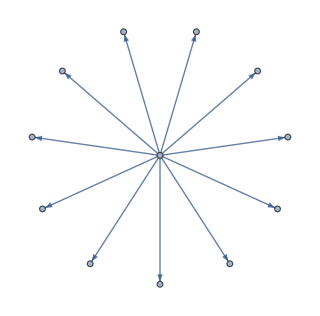
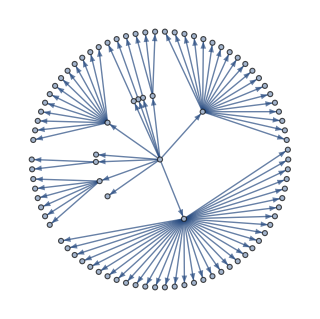
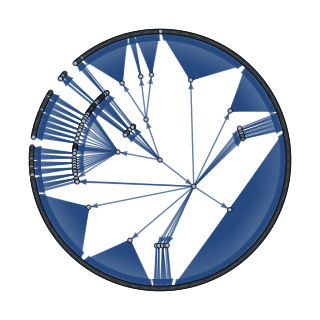
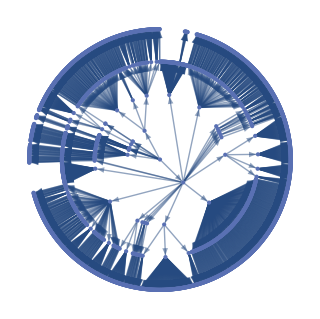
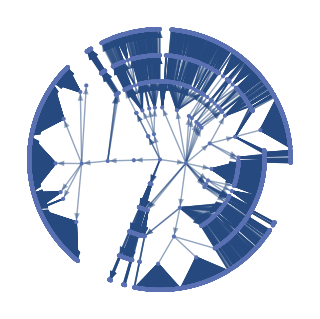
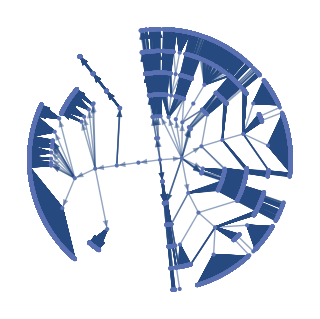

```mathematica
Row@Table[NestGraph[FileNames["*",#]&,$InstallationDirectory,n,GraphLayout->"RadialDrawing",ImageSize->320],{n,6}]
```

## 2 Quilt Pattern

### Manuel Odendahl

a pretty quilt pattern for my girlfriend

```mathematica
ImageCollage[Table[Image@Table[ColorData["CherryTones"]@Mod[Sin[(i-10)( j-10)]^2+m,1],{i,20},{j,20}],{m,0,5,.35}],Automatic,800]
```

-Graphics-

## 3 Poll Map

### Manuel Odendahl

an up-to-date poll map for the upcoming presidential election

```mathematica
GeoGraphics[{If[#[[5]]>#[[6]],Blue,Red],Polygon@#[[3]]}&/@SemanticImport["https://t.co/bJR53g3vyu"][GroupBy@"State",First]]
```

-Graphics-

## 4 Neural Hypnosis

### Michael Sollami

```mathematica
i=RandomImage[];
Dynamic@Magnify[i=NetInitialize[NetChain[{ConvolutionLayer[3,3],Tanh},"Input"->"Image","Output"->"Image"]]@i,3]
```

-Graphics-

## 5 Divisors Tree

### Daniel George

Based on the divisors tree problem at the live coding competition

```mathematica
Manipulate[n//.x_/;!PrimeQ@x&&x>1:>ToString@x@@(Nearest[Divisors@x,Sqrt@x][[1]]^{1,-1}{1,x})//TreeForm,{{n,10^5},1,10^6,1}]
```

## 6 Mickey Mousical

### Philip Maymin

Mickey Mousica! Release your inner magical mouse. (Do your ears hang low? Do they wobble to and fro? Do they resize all about, as you move both in and out?)
(I don’t know if newer webcams will have different dimensions, so you can fiddle with the 400 if need be, Dear Future Code Reader.)

```mathematica
Dynamic@Quiet@Check[{{{a,b},{c,d}}}=FindFaces[i=CurrentImage[]];HighlightImage[i,{Black,PointSize[(d-b)/400],{a,d},{c,d}}],i]
```

-Graphics-

## 7 Circle Pong

### Philip Maymin

Circle Pong! A fully functional tweetable game. Shorter, rounder, and more fun than the original.

Protip: bonus points for slicing! If you just wait patiently for your score to come to you, yeah, you’ll get a point or two. But if you wait to swoop in with a slice at the last moment, or even better just a little late, when the number can smell its freedom, well, then, wrangler, you get yourself some extra mega bonus points! 

Can you get to 1,000 points before your score escapes your corral??

Notes: feel free to lower the 999 number for a more advanced challenge. And be sure to grab the locator ASAP, otherwise you’ll be punished with an ever-expanding bird’s-eye-view of your humiliating and crushing loss, and you’ll have to restart the code to redeem yourself.

```mathematica
p=x={i=0,1};Graphics[{Circle[],Dynamic@Inset[i,x+=If[Norm[p-x]<.1,d=ReIm[E^(i++I)]-x,d]/999.],Locator@Dynamic[p,(p=#/Norm@#)&]}]
```

-Graphics-

## 8

### Richard Gass

```mathematica
URLExecute/@("http://lanl.arxiv.org/abs/"<>#&/@StringCases[URLExecute["http://tinyurl.com/jphk6co"],"arXiv:"~~x:NumberString])
```

## 9 Country Cloud

### Philip Maymin

Country Cloud. Displays the Word Cloud of the important words in the country’s Wikipedia article, in the shape of the country.

```mathematica
Manipulate[Quiet@WordCloud[DeleteStopwords@WikipediaData@✓,ColorNegate@✓@"Shape"],{✓,CountryData[]},SynchronousUpdating->False]
```

## 10

### Nicholas Teague

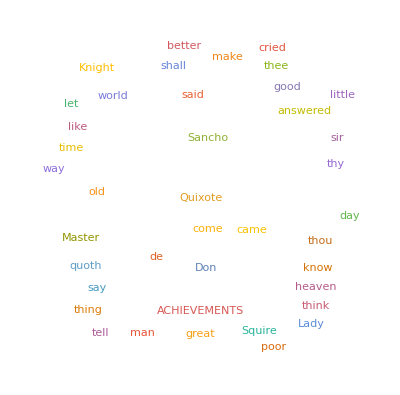

```mathematica
WordCloud[DeleteStopwords@ServiceConnect["OpenLibrary"]["BookText",{"BibKeys"->{{"OLID","OL24156468M"}}}][1],MaxItems->40]
```

## 11

### Richard Gass

```mathematica
Manipulate[ParametricPlot3D[{Sin[λ x]/x, Cos[λ x]/x,Sin[x]}, {x,-10,10},ColorFunction->Hue,Boxed->False,Axes->None],{λ,5,10}]
```

## 12

### Merhan M. Altayeb

In the attached submissions I used sound/speak, graphic, animation, and user Interactivity.

When the notebook is evaluated:

1- A page form pops and the user can input any Country.
2- It will show a geographic map of that Country.
3- When the user hovers over the geographic map it will show a flag for that Country.
4- There is a button next the geographic map. When the user hits it, it will speak wikipedia information related to that Country.

```mathematica
(* Hi, Enter any Country and pop up the volume :) Enjoy *)
```

```mathematica
FormPage[{"n"->"Country"},Button["Wiki",Speak@WikipediaData@#n]
MouseAppearance[DynamicGeoGraphics@#n,CountryData[#n,"Flag"]]&]
```

n | 
 | 

Wiki -Graphics-

## 13

### Merhan M. Altayeb

When the notebook is evaluated:

1- A page form pops and the user can input any City.
2- It will show a geographic map of that City.
3- When the user hovers over the geographic map it will show a clock gauge displaying current time of that City.
4- There is a button next the geographic map. When the user hits it, it will speak wikipedia information related to that City.

```mathematica
(* Enter a City, it gets dynamic! *)
```

```mathematica
FormPage["n"->City,Button[Wiki,Speak@WikipediaData@#n]
MouseAppearance[DynamicGeoGraphics@#n ,Dynamic@ClockGauge@LocalTime@#n]&]
```

## 14 Happy Halloween!

### Abby Brown

Please note the use of the function Nothing to take advantage of the default color palette to make the stem green.

I’m also proud of creating the equations for the pumpkin on my own.

Note that Axes->0 remarkably did not produce an error message for me allowing the removal of the numbers around the Graphics3D box. If that does produce an error, please just delete that option or let me know and I’ll just submit with the axes values and a lower character count. Thanks.

```mathematica
SphericalPlot3D[{(Cos[20t]+70)(p(Pi-p+.1))^.2,Nothing,If[p<.2,90Cos[7p]]},{p,0,Pi},{t,0,2Pi},Mesh->None,PlotPoints->80,Axes->0]
```

-Graphics3D-

## 15

### David Debrota

```mathematica
TableForm[Partition[Drop[CharacterRange[8592,8601],{5,6}][[1+RealDigits[E,8,10^4][[1]]]],100],TableSpacing->{0,0}]
```

→ | ↗ | ↗ | ↙ | ↘ | ← | ↗ | → | ↑ | ↓ | ← | ↗ | ← | ↗ | ↓ | ↗ | ↗ | ↑ | → | ↖ | ↘ | ↗ | → | ↙ | ↙ | ↓ | ↖ | → | ↗ | ↖ | → | ← | ← | ↖ | ↙ | ↑ | ↙ | → | ↓ | ↘ | ↓ | ↘ | ↑ | ↘ | ↘ | ↑ | ↓ | ↖ | ↙ | ← | ↗ | ↖ | ← | ↙ | ↖ | ↙ | ← | ↗ | ↗ | ↑ | ↗ | ↗ | ↑ | → | ↘ | ↗ | ↑ | ↙ | ← | → | ↓ | ↓ | ↑ | ← | ↑ | ← | ↗ | ← | ↘ | → | ← | ↘ | ↓ | ↙ | ↘ | ↙ | ↖ | ↘ | → | → | ↓ | ↖ | ↙ | ↓ | ↖ | ↙ | ← | ↖ | ↖ | ↖
↘ | ↘ | ↓ | ↙ | ↓ | ↙ | ↑ | ↓ | ↙ | → | → | ↙ | ↙ | ↖ | ↓ | ↓ | ← | ↘ | ↘ | ↑ | ↖ | ↑ | ↖ | ↓ | ↗ | ↓ | ↗ | ↖ | ↓ | ↘ | ↘ | ↖ | ← | ↓ | ↓ | ↑ | ← | ← | → | ↗ | ↓ | ↗ | ↖ | → | ↑ | ↖ | ↑ | ↓ | ↘ | ↗ | ↗ | ↑ | ↙ | ↓ | ↙ | ← | ↙ | ↗ | ↗ | → | ↙ | → | ↗ | ↙ | ↙ | → | ↘ | → | ↗ | ↖ | ↑ | ↑ | ↑ | ← | ↓ | ↑ | ↙ | ↘ | ↗ | ← | ↙ | ↘ | ↗ | ↙ | ↖ | ← | ↘ | ↓ | ↓ | ↗ | ↗ | ← | → | ← | ↗ | ↓ | ← | ↘ | ↘ | →
↗ | → | ↗ | ↑ | ↙ | ↓ | ↘ | ↘ | ↖ | ↓ | → | ↙ | ↖ | ↙ | ↓ | → | ↗ | → | ↙ | ← | ↖ | ↘ | ↗ | ↙ | ↑ | ↙ | ↙ | → | ↗ | ↙ | ↖ | ↖ | ↖ | ↘ | ↗ | ↖ | ↘ | ← | ↖ | ↙ | ↖ | ↑ | ↖ | ↓ | ↖ | ↑ | ↘ | ← | ↓ | ↖ | ↘ | ↖ | → | ↘ | ↙ | ↓ | ↙ | ↖ | → | ↗ | ↑ | ↗ | ← | ↖ | ↙ | ↓ | → | ↙ | ↖ | ↙ | ↘ | ↙ | ↙ | ↗ | ← | ↓ | ↖ | ↖ | ↑ | ↘ | ↙ | ↘ | ↑ | → | ↘ | ↑ | → | ← | ↖ | ↘ | ↘ | ↗ | ↓ | ↓ | ↘ | ↓ | ↖ | ↘ | ↗ | ↑
↖ | ↑ | → | ↘ | ↓ | ↑ | → | → | ↓ | ↘ | ↖ | ↖ | ← | ↙ | → | ↓ | ↘ | → | ↙ | ↗ | → | ↙ | ↖ | ← | → | ↗ | ↓ | ← | ↘ | ← | → | ↗ | ↖ | ↘ | → | → | ↓ | ↙ | ↓ | ↓ | ← | ↓ | ↗ | ← | ↖ | ↑ | ← | ↗ | → | → | ↖ | ↗ | ↘ | ↘ | → | ↘ | → | ↑ | ↘ | ↑ | ↙ | ↙ | ↓ | ↗ | ↘ | → | ↘ | ↗ | ↓ | ↓ | → | ↗ | ↗ | ↘ | ↘ | ← | ↓ | → | ↙ | ↙ | ↗ | ← | ↘ | ↖ | ← | ↓ | ↗ | → | ↓ | ↘ | ↖ | ↑ | → | ↖ | ↓ | ↘ | ↙ | ↖ | ↓ | ↖
↗ | ↑ | ↗ | ↙ | ↗ | ↑ | → | ↙ | ↑ | → | ↘ | ↙ | ↓ | ↓ | ↘ | ↓ | ↗ | ↖ | ↓ | ↓ | ↖ | ↗ | ↓ | ↗ | ↖ | ↓ | ↑ | ← | → | ↘ | ← | ↓ | ↘ | ↖ | ↙ | ↘ | → | ↑ | ↘ | ↙ | ← | ↑ | → | ↓ | ↓ | → | ↙ | ← | → | ↓ | ↘ | ← | ← | ↗ | ↙ | ↘ | ↓ | ↖ | ↑ | ↘ | ↓ | ↓ | ↙ | ↓ | ↙ | ↖ | → | ↙ | ↓ | ↑ | ↖ | ← | ← | ↘ | ↖ | ← | ↑ | ↑ | ↖ | ↘ | ↖ | ↗ | ← | ↑ | ↗ | ← | → | ↙ | ↗ | ↖ | ↑ | ↖ | ↖ | → | ↙ | ↑ | ↓ | ↙ | ↘ | ↖
↙ | ↑ | ↘ | ↖ | ↘ | ← | ↗ | ↖ | ← | ↙ | ↙ | ↙ | ↘ | ↑ | ↘ | → | ↓ | ↘ | ↑ | ↑ | ← | ↘ | → | ↙ | ↓ | ↗ | ↙ | ↑ | → | ← | ↑ | ↖ | ← | ↙ | ↖ | ↑ | ↙ | ↙ | ↘ | ↑ | ↘ | ↘ | ↑ | ↗ | ↗ | ↑ | ↖ | ↓ | ↓ | ↙ | → | ↘ | ↗ | ↘ | ↓ | ↑ | ↘ | ↙ | ↓ | → | ↙ | ↙ | ↖ | ↗ | ↙ | ← | → | ↙ | ↓ | ← | → | ↑ | ← | ← | ← | → | ↙ | ← | ↗ | ↖ | ↓ | ↗ | ↙ | ← | ↘ | ← | ↓ | ↓ | ↙ | → | ↑ | ↓ | → | ← | ↓ | ↗ | ↖ | ↗ | ↖ | ↓
↓ | ↘ | ↓ | → | → | ↖ | → | ↓ | ↓ | ← | ↑ | ↗ | ↖ | ↗ | ↘ | ↙ | ↙ | ↙ | → | ↖ | → | ← | ↘ | ↗ | ↗ | ← | → | ↑ | ↘ | ← | ↘ | ← | ↖ | ↓ | ↙ | ↘ | ↓ | ↙ | ↗ | ↘ | ↓ | ↓ | ↘ | ↑ | ↗ | → | ↗ | ↗ | ↖ | ↙ | ↓ | ↓ | ↑ | → | ↑ | ↖ | ↖ | ← | ↓ | → | ↘ | ↙ | ↓ | ↘ | ← | ↘ | ↖ | ↙ | ↗ | ↑ | ↗ | ↙ | ↓ | ↙ | ↑ | ↖ | ↙ | ← | ← | ↑ | ← | ↙ | ← | ↓ | ← | ↓ | ↓ | → | ↑ | ↗ | ↙ | ↘ | → | ↓ | ↗ | ↓ | ↓ | ↖ | ↘ | ↘
→ | → | ← | ↓ | ↗ | ↙ | → | ↘ | ↘ | → | ↑ | ↘ | ↖ | ↖ | ↘ | ↖ | ↖ | ↓ | ↙ | ↓ | ↙ | ↘ | ↙ | ↙ | ↓ | ↖ | ↗ | ↖ | ↘ | ↑ | ↖ | ↗ | ↖ | ↑ | ↙ | ↗ | ↓ | ← | ↑ | ↖ | ↑ | ↗ | ↗ | ↖ | ↖ | ↓ | ↖ | ↗ | ↓ | ↗ | ↙ | ↙ | ← | → | ↓ | ← | → | ↓ | ← | → | ↖ | → | ↓ | ↖ | ↖ | ↖ | ↙ | ← | → | ↘ | ↖ | ← | ↖ | ↘ | ← | ↘ | → | → | ↓ | ↗ | ↙ | ← | ↖ | ↑ | ↗ | ↙ | ↑ | → | ↑ | ↑ | ↙ | → | ↓ | ↙ | ↗ | → | ↑ | ← | ↗ | ↑
↓ | ↖ | → | ↘ | ↗ | ↘ | ↖ | ↘ | ↙ | → | ↓ | ↓ | ↑ | ↑ | ↙ | ↑ | ↓ | ↖ | → | ← | ↙ | ↖ | ↙ | ← | ↙ | ↘ | ↗ | → | → | ↙ | ↙ | ↙ | ↗ | ↓ | ↖ | ↗ | ↓ | ↗ | ← | ↑ | → | ↗ | ↓ | ↖ | ↙ | ↑ | ↑ | ↘ | ↙ | ↘ | ↘ | ↖ | ↙ | ↗ | ↘ | ↖ | ↑ | ↗ | ↗ | ↑ | → | ↙ | ↖ | → | ↖ | ↖ | → | ↑ | ↗ | ↖ | ↓ | ↗ | ← | ↑ | ↗ | ↗ | → | ↙ | ↖ | → | ↖ | ↖ | ↑ | ↖ | ↗ | ↙ | ↑ | ↗ | ↖ | ↑ | ↗ | ↙ | → | ↗ | ↗ | ↗ | ← | ↓ | ↗ | ↗
↙ | ↙ | ↑ | ↗ | ↑ | ← | → | ↘ | ↗ | ↓ | ↖ | → | ↑ | ↑ | ← | → | ↓ | ↖ | ← | ↗ | → | ↙ | ↖ | ↘ | ↖ | ← | ↘ | ↗ | ↙ | ↙ | → | → | ↖ | ↙ | ↗ | ↘ | ↙ | ↗ | ↙ | ↑ | ↙ | ← | ↑ | ↗ | ↖ | ↖ | ← | ↙ | ↓ | ↖ | ↓ | ↙ | ↙ | → | ↗ | ↖ | ↙ | → | ↙ | ↘ | ← | ↖ | ↗ | ↙ | ↑ | ← | ↑ | ↘ | ↖ | ↗ | ↓ | ↓ | ↑ | ↗ | ↑ | ↙ | ← | ↓ | ↘ | ↙ | ↖ | → | ↘ | ↙ | ↑ | ↗ | ↙ | → | ↖ | ↗ | ↖ | ↑ | ↖ | → | ↘ | → | ↓ | ↓ | ↙ | →
↓ | ↙ | ↓ | ↓ | ↘ | → | ↓ | ← | ↓ | ↗ | ↑ | ↙ | ↑ | ↑ | ↘ | → | ↘ | ↑ | ← | → | ↗ | ↙ | ↓ | ↓ | → | ↗ | ↖ | ↓ | ↙ | → | ↗ | ↙ | ↗ | ← | → | ↘ | ↗ | ↗ | ↑ | ↙ | ↗ | ↗ | ↗ | ← | ↘ | ← | ↙ | ↓ | ↗ | ↖ | ↓ | ↘ | ↓ | ↘ | ↑ | ↘ | ↗ | → | ↗ | ← | ← | ↘ | ↖ | ← | ← | ← | ↖ | ↖ | ↑ | ↙ | ↙ | → | ↗ | ↓ | ↓ | ↗ | ↑ | → | ↙ | ↙ | ← | ↘ | ↑ | ↘ | ↓ | ← | ↙ | ↗ | ↑ | ↘ | ↑ | ↑ | ↗ | ↓ | ↖ | ↖ | → | ← | ↘ | ↙
↓ | ↙ | ↓ | → | ← | ↘ | ↑ | ↖ | → | ↗ | ↘ | ↘ | ↗ | ↗ | → | ← | ↙ | ↖ | ← | ← | ↖ | ↗ | ↗ | ↖ | ↙ | ↖ | ↘ | ↖ | ← | ↘ | → | ↗ | → | → | ← | ↓ | ↗ | ↖ | ← | ← | → | ↗ | ↑ | ← | ↘ | ← | ↑ | ↑ | ↖ | ↑ | ↖ | → | ↑ | ↗ | ↗ | ↘ | ↑ | ↘ | ↙ | ↖ | ↓ | ↙ | ↑ | ↓ | ↖ | ↓ | → | ↘ | ↖ | ← | ← | ↑ | ↘ | ← | ← | ↖ | ↖ | ↗ | ↑ | ↖ | ↘ | ↓ | → | ↑ | ↖ | ↘ | ↓ | ↘ | → | ↙ | ← | ↗ | ↗ | ↙ | → | ← | ↘ | ↖ | ↑ | ↘
↘ | ↙ | ↑ | ↑ | ↙ | → | ↙ | ← | ↗ | ← | ← | ← | ← | ← | ↓ | ↘ | ← | ↗ | → | → | ↓ | ↗ | ↖ | ↙ | → | ↗ | ↑ | ↙ | ↘ | ↓ | ← | ↘ | ↖ | ↑ | → | ↘ | ↓ | ← | ← | ↗ | → | ← | → | ↖ | ↖ | ↓ | ↖ | ↘ | ↙ | ↑ | ↘ | ↘ | → | → | ↙ | ↘ | ↙ | ↑ | ↙ | ↖ | ↓ | ↗ | ↖ | ↖ | ↘ | ↘ | ↗ | → | ↘ | ↖ | ↙ | ↙ | ↘ | ↑ | ← | ↗ | ↑ | ← | ↘ | ↗ | ↗ | ↑ | ↗ | ↗ | ↗ | ↓ | → | ↖ | ↑ | → | ↑ | ↙ | ↗ | ← | ↖ | ← | ↘ | ← | → | ↙
← | ↓ | ↖ | ↓ | → | ↑ | → | ← | ← | ← | ↙ | ↙ | ↑ | ↓ | ↘ | ← | ↓ | ↓ | ↗ | ↖ | ↖ | ← | → | ← | → | ↙ | ↙ | ↘ | ↗ | ↖ | ↖ | ↗ | ↗ | ↖ | ↖ | → | ↖ | ← | ↓ | ↓ | ↓ | ← | ↙ | ↗ | ↑ | ↑ | ↘ | ↓ | ↑ | ↘ | ↙ | ↘ | ↖ | ↗ | ↖ | ↑ | ↘ | ← | ↗ | ↑ | ↖ | ↗ | → | ↑ | ↘ | ↖ | → | ↑ | ↘ | ↙ | → | → | ↑ | ← | ↖ | ↑ | ↓ | ↑ | → | ↙ | ↗ | → | ↓ | ↙ | → | ↖ | ↘ | ↑ | ↘ | ↙ | ↓ | → | ↑ | → | ↖ | ↑ | ↖ | ↗ | ↑ | ↗
↗ | ↘ | ↘ | ↑ | ↑ | ↑ | ↖ | ↖ | → | → | ↑ | ↓ | ↘ | ↙ | ↗ | ↘ | ↗ | ↖ | ↖ | ↗ | ↖ | ↓ | ↖ | ← | ↓ | ↙ | ↗ | → | ↓ | ↑ | ↓ | ↑ | ↘ | ↑ | ↘ | ↖ | ↓ | ← | ↓ | ↑ | ↗ | ↑ | ↖ | ↓ | ↖ | ← | ↑ | ↘ | ← | ↙ | → | ↘ | ↓ | ↓ | → | ↘ | ↖ | ← | ↘ | → | ↗ | ↙ | ↙ | ↘ | ↓ | ↑ | ↙ | ↙ | ↓ | ← | ↙ | ← | ↘ | ↓ | ↓ | ← | ↙ | ↘ | ↗ | ↘ | ← | ↙ | ↘ | → | ↓ | ↖ | ↖ | ↓ | ← | ← | ↖ | ← | ↙ | ↘ | ↓ | ↖ | → | ← | ↑ | →
↑ | ↙ | ↙ | ↗ | ↗ | ↑ | ↖ | ↙ | ↙ | ↓ | ↓ | → | ↑ | ↘ | ↙ | ↗ | ↑ | → | → | → | ↑ | ↘ | ↑ | ↙ | ↗ | ↙ | → | ↖ | ↘ | ↗ | ↑ | ↓ | → | → | ↑ | ← | → | ↙ | ← | → | ↗ | → | ↓ | ↑ | ← | ↗ | ↘ | ↘ | ↘ | ↘ | ↘ | ↑ | ↗ | ← | ← | ↘ | ↘ | ↑ | → | ← | ← | ↑ | ↘ | ↙ | ↖ | ↑ | ↑ | ↑ | ← | ↘ | ↗ | ← | ↑ | → | ↑ | ← | ↙ | ↖ | ↓ | ← | → | ↗ | ↓ | ↙ | ↓ | ← | ↑ | ↙ | ↙ | ↙ | ↙ | ↖ | ↙ | ↖ | ↓ | ↗ | ← | ↖ | ↘ | ↙
↑ | ↙ | ↙ | ↗ | ↖ | ↗ | ↑ | ↙ | ↘ | ↑ | ↖ | ← | ↘ | ← | ↓ | ← | ← | ↖ | ↓ | ↘ | ← | ↘ | ↗ | ↖ | ↑ | ↙ | ↘ | ↑ | ↘ | ↑ | ↗ | ↗ | ← | ← | ← | ↓ | ↗ | ↙ | ↗ | ↖ | ↘ | ↘ | ↖ | ↓ | ↗ | ↖ | ↓ | ↙ | ↑ | ↑ | ↘ | → | → | ↙ | ↑ | → | → | ↘ | → | ↗ | ↘ | ↙ | ↖ | ← | ↘ | → | ↖ | ↘ | ↑ | ↖ | ↘ | → | ↖ | ↓ | ↘ | ↓ | ↗ | ↙ | ↖ | ↗ | ↓ | ↙ | ↑ | ↖ | ↖ | ↗ | ↘ | ↙ | → | ↗ | → | ↘ | ← | ← | → | ↑ | ↖ | ↗ | → | ↑
→ | ← | ↑ | ↗ | ↙ | ↘ | ↘ | ↗ | ↖ | ↙ | → | ↓ | ↖ | ↙ | ↑ | ↘ | ← | → | → | ↑ | ↑ | ↖ | ↑ | ← | ↗ | ↗ | ← | ↑ | ← | ↑ | → | ↙ | → | ↑ | ↗ | ↗ | ↗ | ↓ | ← | → | ↑ | ↙ | → | ↓ | ↑ | ↙ | ↖ | ↗ | ↙ | ↗ | ↙ | ↖ | ↙ | ↑ | ↑ | ← | → | → | ↑ | ↗ | ↗ | ← | ↘ | ↑ | ↓ | → | ↗ | ↑ | ↘ | ↑ | ↖ | ↘ | ↗ | ↘ | → | ↗ | ↖ | ← | ↓ | ↓ | ↗ | ← | ↘ | ↗ | ↓ | ↖ | ↙ | ↓ | ↙ | ↘ | ↗ | ↙ | ↑ | ↖ | → | ↑ | → | → | → | ↘
← | ↘ | ↑ | ← | ↗ | → | ↘ | ↑ | → | ↗ | ← | → | ↑ | ↖ | ↗ | ← | ↑ | ↓ | ↗ | ↘ | → | ← | → | ↘ | ↘ | ↙ | ← | → | ↗ | ← | ↓ | ↑ | ↘ | ↑ | → | ↙ | ↑ | ↑ | ↑ | ↙ | ↗ | → | → | ↑ | ↗ | ↓ | ↖ | ↖ | ↗ | ↓ | ↓ | ↖ | ↖ | → | ↑ | ↓ | ↘ | ↑ | ↖ | ↘ | ↓ | ↘ | → | ↘ | ↙ | → | ↗ | ↘ | → | ↗ | ↖ | ↙ | ↓ | ↘ | ↖ | ← | ← | ↙ | ↘ | ↘ | → | ↓ | ↗ | ← | ↘ | ← | ↑ | ← | ↓ | ← | ↘ | ↑ | ↑ | ↘ | → | ↗ | ↖ | ← | ↖ | →
↘ | ↘ | ↓ | ↗ | ↗ | ↘ | ↑ | ↙ | ↘ | ↓ | ↗ | ↘ | ↑ | ↗ | ↓ | ↖ | ← | ↑ | ↗ | ↓ | ← | ↙ | ↙ | ↘ | ↙ | → | ↖ | ↗ | → | ↑ | ↘ | ↖ | ↘ | ↗ | ↗ | ↗ | ↖ | ↓ | ↘ | ↓ | → | → | ↘ | ↑ | → | ↖ | ↘ | ↖ | ↗ | → | → | ↓ | ↓ | → | ↖ | ↑ | ↖ | → | ↘ | ← | ↙ | ← | ↑ | ↗ | ↑ | ← | ↑ | ↘ | ↗ | → | ↙ | ← | ↓ | → | ↙ | ↖ | ↖ | ↙ | ← | ↘ | ↘ | ↗ | ↗ | → | → | ↖ | ↖ | ← | ↓ | ↖ | ↓ | ↑ | → | ↓ | ↖ | ↘ | ↓ | ↙ | ↙ | →
↑ | ↗ | → | ↗ | → | ↖ | ↓ | ↓ | → | ↗ | ↗ | ← | ← | ← | ↖ | ↘ | ↓ | ↘ | ↘ | ← | ← | ↑ | ↖ | ↖ | ← | ↙ | ← | ← | ↙ | ↖ | ↖ | ↑ | ↑ | ↓ | → | ↑ | ↖ | ↓ | ↗ | ↖ | ↗ | → | ↑ | ↗ | ↓ | ↖ | ↘ | → | ↓ | ↙ | ↗ | ↗ | ↖ | ↖ | ↓ | ↙ | ↙ | ↑ | ↘ | ↘ | → | → | ↗ | ← | → | ↓ | ↗ | → | ← | ↘ | ↘ | ↖ | ↑ | ↙ | ↙ | ↙ | → | ↘ | ↘ | ↖ | ↙ | ↗ | ↗ | ↘ | ↖ | ↓ | ↖ | ↘ | ↑ | ↓ | ↘ | ← | → | ↙ | ← | ↘ | ↓ | ← | ↓ | ↗
↙ | ↓ | ↙ | ↓ | ↑ | ↑ | ↓ | ← | ↖ | ↑ | ↘ | ↙ | ↘ | ← | ↘ | ↗ | ↗ | ↖ | ↓ | ← | ↗ | ← | → | ↗ | ← | ↙ | → | ↗ | ↘ | ↑ | ← | ↑ | → | → | ↗ | → | ↗ | ↓ | ↓ | ↑ | ↓ | ↘ | ↙ | → | ↑ | ↙ | ↖ | ↖ | ↖ | ↘ | → | ↓ | ↑ | ↖ | ↗ | ↘ | → | ↘ | → | ↘ | ← | ↑ | ↙ | ← | ↙ | ↑ | ↖ | ← | ← | ↓ | ↓ | ↘ | ↗ | ↘ | ← | ↑ | ← | ↗ | ↑ | ↑ | ↘ | ↑ | ← | ↖ | ← | ↙ | ↑ | ↘ | ↖ | ↗ | → | ↙ | ↖ | ← | ↗ | ↙ | ↑ | ← | ↗ | →
↑ | → | ← | → | → | ↗ | ↖ | ↓ | ↘ | ↑ | ↓ | ↓ | ↗ | ↓ | ← | ↑ | → | ← | → | ↑ | → | ← | ↖ | ↓ | ↓ | ← | ← | ↗ | ↘ | ↖ | ↓ | → | ↙ | ← | ↓ | → | ↙ | ↘ | ↗ | ↘ | ↑ | ↓ | ↑ | ← | ↗ | ↖ | ← | ↘ | ↓ | ← | ← | → | ↑ | ↗ | ↙ | ↘ | ↘ | ← | → | → | ↖ | → | ↗ | → | ← | ↓ | ↙ | ↘ | ↑ | ↗ | ← | ↘ | → | ↓ | ↖ | ↖ | ↑ | ↗ | ↓ | ← | ← | ↖ | → | ↗ | ↘ | ↘ | ↙ | ← | → | ↓ | ↑ | ↖ | ↑ | ↘ | ↘ | ↗ | ↑ | ← | ↘ | ←
↓ | ↖ | ↙ | → | ↑ | → | ↑ | ↗ | → | ↑ | → | ↖ | ↖ | ↘ | ↑ | ← | → | → | ↙ | ← | ← | ↙ | ↙ | ↙ | ↓ | ↖ | ↑ | ↘ | ← | ↖ | ↑ | ↓ | ↙ | ↖ | ↘ | ↘ | ← | ↙ | ← | ↑ | ↑ | ↗ | ↘ | → | ↖ | ↗ | ↖ | → | ↖ | ↓ | → | ↗ | ↑ | ↗ | ↑ | ← | ↙ | ↖ | ← | ↙ | ↑ | ← | → | ↑ | ↙ | ↑ | ↙ | ↘ | → | ↓ | ↑ | ↙ | → | ↓ | ↘ | ↑ | ↖ | → | ↘ | → | ↖ | ↑ | ↖ | ← | ↖ | ↖ | ↑ | ↓ | ↘ | ↘ | ↘ | ↑ | ↑ | ↑ | ← | ← | ↗ | ↗ | ↖ | ↘
↘ | ↗ | ↗ | ↖ | ↘ | ↗ | ↑ | → | ↙ | ↙ | ↑ | ↘ | ↗ | ↓ | ↓ | ↖ | ← | ← | ↑ | ↖ | ↗ | ↑ | ← | ↖ | ↓ | ↓ | ↑ | ↘ | ← | ↑ | → | ← | → | ↖ | ↑ | ↙ | ↙ | ↖ | ↓ | ← | ↑ | ↘ | ↗ | ↗ | ↑ | → | ↙ | ↓ | ↙ | ↖ | → | ↑ | ↖ | ↓ | ← | ↑ | ↙ | ↙ | ← | ← | ↙ | → | ↖ | ↗ | ← | ↙ | ↙ | ↑ | ↓ | ↙ | → | → | ↑ | → | ↙ | ← | ↙ | ↗ | ↙ | ↘ | → | ↑ | ↖ | ↙ | ← | ↑ | ↓ | ↗ | → | ↑ | → | → | ↓ | ↙ | ↘ | ↖ | → | ↘ | ↘ | ↖
↑ | → | ↗ | ↘ | ↙ | ↙ | ↘ | ↓ | ↖ | ↗ | ↓ | ← | → | ↖ | ↘ | ↓ | ↓ | ↗ | ↗ | ↙ | ↓ | → | → | ↙ | ↘ | ↙ | → | ↗ | ↙ | ↙ | ↓ | ↙ | ↑ | ↓ | ← | ↗ | ← | ↘ | ← | ↙ | ↘ | ↗ | ↙ | ↗ | → | ↙ | ↘ | ← | ↙ | ← | ↗ | ↘ | ↗ | ↘ | ↑ | ↗ | → | ← | ↙ | ↙ | ← | ↗ | ↙ | ↓ | ↗ | ← | ↑ | ↙ | ↓ | ↙ | ← | ↘ | ← | ↓ | ↙ | ↙ | → | ← | ↘ | ↙ | ↙ | ↗ | → | ↓ | → | ↙ | ↓ | ↙ | ↙ | ↓ | ↘ | → | ↖ | ↘ | ← | ↓ | ↑ | ↘ | ↙ | ↙
↖ | ↑ | ↗ | ↖ | ↗ | ↙ | ↗ | ← | ↖ | ↓ | ↗ | → | → | ↓ | ↙ | ↓ | ↘ | ↗ | ← | → | ↑ | ← | ↓ | ↘ | ↖ | ↑ | ← | ↑ | ← | ↗ | ↘ | → | ↖ | ← | ↘ | ↗ | → | ↓ | ↙ | → | ↑ | ↖ | ↑ | → | ↓ | ↖ | ← | ← | ↖ | ↓ | ↘ | ↑ | → | ↗ | ↑ | → | → | ← | ↓ | ↖ | ↓ | ↙ | ↙ | ↖ | → | ↑ | ↖ | ↘ | ↗ | ↗ | ← | ↘ | → | ↑ | ↓ | ↗ | ↗ | ↙ | ↖ | → | ↖ | ↓ | ↘ | ↙ | ↓ | ↘ | ↘ | ↘ | ↗ | ↑ | ↑ | ↙ | → | ↗ | ← | ↗ | → | ↘ | ↖ | ↙
↖ | ↗ | ↖ | ↑ | ↙ | ↓ | ↙ | → | ↘ | ↙ | ↓ | → | ↓ | ↖ | ← | ↓ | ↖ | ↘ | ↗ | ↗ | → | ↘ | ← | ↘ | ↗ | ↗ | ← | ↓ | ↗ | ↑ | ↑ | ↑ | ↓ | ↙ | ↘ | ↑ | ↑ | ↗ | ↗ | ↘ | ↗ | ← | ← | ↓ | ↑ | ↓ | ← | ← | ↗ | ↗ | ↓ | ↗ | ↘ | ↖ | ↙ | ↓ | ↙ | ↗ | → | ↙ | → | → | ↙ | ↑ | ↙ | ↘ | ↓ | ↗ | ↗ | ← | ← | ↘ | ↓ | ↗ | ↘ | ↖ | → | ← | ↖ | ← | → | ↗ | ← | ↑ | ↓ | ↘ | ↘ | ↙ | ↘ | ↑ | ↘ | ↘ | ↖ | ↖ | ↙ | → | ↙ | ↑ | ↑ | ↘
→ | ↙ | ↘ | ↑ | ↑ | ↙ | ← | ↑ | ↑ | ↘ | ↖ | ← | ← | ↖ | ↓ | ↖ | ↗ | ↘ | ↗ | ↓ | ↓ | ↘ | ↘ | ↓ | ↑ | ↑ | ← | ↙ | ↑ | ↑ | ↗ | ↖ | → | ↖ | ↑ | ↖ | ↑ | ↙ | → | ↘ | ↖ | ↑ | ↑ | ↖ | → | ↖ | ↗ | ↙ | ↖ | → | ↘ | ← | ↖ | ← | ↖ | ↙ | ↑ | ↓ | ↗ | → | ↑ | → | ↗ | ← | ↙ | ↑ | ↙ | ↑ | ↙ | ↑ | → | ↖ | ↓ | ↘ | ↗ | ↗ | ↗ | ↙ | ↑ | ↓ | ← | ↘ | ↑ | ↑ | ↓ | ↗ | ↖ | ↓ | ↓ | ↖ | ↖ | ↓ | → | ↘ | ↘ | → | ↙ | ↗ | → | ↙
↙ | ← | ← | ↗ | ← | ↙ | → | → | ↘ | ↓ | ↑ | ↓ | ↗ | ↗ | ↑ | ↑ | ↘ | ↘ | ↓ | ↗ | ← | ← | ↓ | ↓ | ↗ | ↘ | ← | → | ↓ | ↙ | ← | ↑ | ↗ | ↙ | ↗ | ← | ↓ | ↑ | ← | ↗ | ↘ | ↘ | ↘ | ↖ | ← | ↙ | ↙ | → | ↓ | ↖ | → | ↓ | ↓ | ← | ↗ | ↘ | ↗ | ↙ | → | ↑ | ↗ | ← | ↖ | ↑ | ↗ | ← | → | ↑ | ↖ | → | ↖ | ↖ | ↓ | ← | → | ↖ | ↘ | ↗ | ↗ | → | ↙ | ↓ | ↓ | ↑ | ↑ | → | ↓ | ↙ | ↖ | → | ↖ | ↗ | ↓ | → | ↓ | ↖ | ↙ | → | → | ↘
→ | ↙ | ← | ↘ | ↖ | ↑ | ← | ↑ | ↘ | ↖ | ↖ | ← | → | ↘ | → | ← | → | ↙ | ↓ | ↖ | ↙ | ↗ | ↓ | ↗ | ↓ | ↖ | ← | ← | ↗ | ↘ | ← | ↗ | ↘ | ↗ | ↗ | ↘ | ↘ | → | ↖ | → | ↙ | ↙ | → | ↗ | ↓ | ↙ | ↙ | ↙ | ↓ | ↖ | ↑ | ↘ | ↙ | ↓ | ↖ | ↘ | ↙ | ↖ | ↓ | ← | ↓ | ↖ | ← | ← | ↘ | ↘ | → | → | ↑ | ↘ | ↖ | ← | ↙ | ↙ | ↖ | → | ← | ↖ | ↙ | → | ↘ | ↓ | ↗ | → | → | ↓ | ↙ | ← | ↑ | ↖ | ↑ | → | ↘ | ↖ | ← | ↘ | ↖ | → | → | ←
↑ | → | ↗ | ↑ | ↗ | ↓ | → | → | → | ← | ↗ | ↖ | ↑ | ← | ↑ | ↘ | ↗ | → | ↘ | ↙ | ↘ | ↙ | ↖ | ↘ | ← | ↗ | ↘ | ← | ← | ↑ | ↑ | ↙ | ↘ | → | ↙ | ↗ | ← | ↗ | ↖ | ← | ↖ | ↙ | ↑ | ↓ | ↑ | ↑ | ↓ | ↗ | ← | ↗ | ↖ | ↗ | ↘ | ↗ | ← | ↘ | ↗ | → | → | ↖ | → | ↓ | ← | ↓ | ↘ | ↗ | → | ↙ | ↓ | → | → | ← | ↗ | ← | ↗ | ↖ | ↖ | ↓ | ↖ | ↗ | ↗ | → | ↑ | ↗ | ↑ | ↗ | ↑ | ↖ | ↘ | ↖ | ← | ↖ | ↖ | ↙ | ↖ | ↖ | ↖ | ↘ | ↗ | ←
↖ | ↗ | ↖ | → | ↗ | ↘ | ↓ | ↖ | ↑ | → | ← | ↗ | ↙ | ↘ | → | ↘ | ↘ | → | ↖ | ↘ | ← | ↓ | ↙ | ↘ | → | ← | ↙ | ↑ | ↗ | ↗ | → | ↙ | ↓ | ↘ | ↗ | ↗ | ← | → | ↘ | ↑ | ↖ | ↘ | ↑ | ↙ | → | ↙ | ← | ↙ | ↖ | ↙ | ↓ | ↖ | ← | ↓ | → | ↗ | ↘ | ↓ | ↑ | ↑ | ↓ | ↙ | ↓ | ↓ | ↑ | ← | ↘ | ↖ | ← | → | ← | → | → | ↙ | ↑ | ↗ | ↙ | ↑ | ↖ | ↙ | ↓ | ↗ | ← | ← | ↖ | ↙ | ↘ | ↗ | ↓ | → | ↗ | ↙ | ↓ | ↖ | ↓ | ↖ | ↗ | ↑ | ← | →
↘ | → | ↙ | ↑ | → | ↖ | ← | ↓ | ↗ | ← | ↓ | ← | ↙ | ↘ | ↖ | → | ↑ | ↖ | ← | ↙ | ← | → | ↙ | → | ↘ | ↘ | ↖ | ↖ | ↓ | ← | → | ↖ | ↖ | ↓ | ↙ | ↖ | ↑ | ↙ | → | ↑ | ↓ | → | ↖ | ↙ | → | ↙ | ↖ | ↑ | ↗ | ↖ | ↘ | ↖ | ↙ | ↗ | → | ↗ | ↖ | ↑ | ↑ | → | → | ↓ | ↘ | ↘ | ↖ | ↓ | ↓ | ← | ↖ | ← | ← | ↖ | ↙ | ↖ | ↑ | ← | ↑ | ↗ | → | ↖ | ↓ | ↖ | ↑ | ↓ | → | → | ← | ↑ | ↖ | ↓ | ↓ | ← | ↗ | ← | ↗ | ↙ | → | ↙ | ↘ | ↑
↘ | ↘ | ↖ | ↖ | ↘ | ↖ | ↓ | ↘ | ↖ | ↓ | → | ↓ | ↑ | ↖ | ↖ | ↑ | ↗ | ↓ | ↓ | ↓ | → | ↙ | ← | ↗ | ↓ | ↓ | → | ↑ | ↙ | ↓ | ← | ↗ | ↙ | ↘ | ↙ | ↓ | ↓ | ↓ | ↓ | ↘ | ↓ | ← | ← | ↙ | → | ↓ | ↗ | ↓ | ↑ | ↖ | → | ↙ | ↘ | ↖ | ↓ | → | ↗ | ↗ | ↗ | ↘ | ↑ | ↗ | ← | ↙ | → | ↖ | ← | ← | ↓ | ↓ | ↖ | → | → | ↘ | ↑ | ↙ | ↘ | ↓ | → | ↙ | ↓ | ← | ↘ | ↙ | ↖ | ↗ | ↙ | ← | ← | ↘ | → | ← | ↙ | ↗ | ↙ | ↗ | → | → | ↘ | ↗
← | ↙ | ↓ | ↖ | ↓ | ↙ | → | ↑ | ↘ | ← | ↙ | ↗ | ← | ↙ | ↑ | ↗ | ↘ | ↗ | ↘ | ↗ | ↑ | ↖ | ↙ | ← | ← | → | ↑ | ↙ | ↗ | ↗ | ↗ | ↓ | ↙ | ↓ | ↓ | ↖ | ↑ | ↑ | ↗ | ↘ | → | ↓ | ↘ | → | ↘ | ↘ | ↙ | ← | → | ↓ | ← | ↘ | ↖ | ↙ | ↑ | → | ↘ | → | ↗ | → | → | ↘ | ↘ | ← | ← | ↘ | ↑ | ↓ | ↙ | ↗ | ↘ | ↗ | ↙ | ↖ | ← | ↖ | ↘ | ↗ | → | ↓ | ↖ | ↑ | ↙ | ↓ | ↖ | ↑ | ↓ | ← | ↑ | ↖ | ↙ | ↗ | ↑ | ↖ | ↗ | ↗ | ↑ | ↙ | ← | ↖
↙ | ↓ | ↑ | ↓ | ↓ | ↙ | ↘ | ↑ | ← | ← | ↙ | ↗ | ↘ | ↗ | → | ↑ | ↓ | ↙ | ↗ | ↖ | ↙ | ← | ↑ | → | ← | ← | ↙ | ↘ | ↘ | ↗ | ← | ↙ | ↑ | ↘ | ↓ | ↑ | ↑ | → | ↙ | ↖ | ↗ | ↑ | ↗ | ↓ | ↑ | ← | ↖ | → | ↙ | ↙ | ↘ | ↓ | ↙ | ↙ | ↓ | ← | ← | ↗ | ↓ | ↓ | ↙ | ↗ | ↗ | ↙ | ↓ | ↖ | ↗ | ↓ | ↑ | → | ↖ | ↗ | ↑ | ↗ | ↙ | → | → | ↘ | ↑ | ↙ | ↓ | ↙ | ↑ | ↓ | ↗ | ↗ | ↗ | ↖ | ↗ | ↓ | ↖ | ← | ↙ | ↘ | ↑ | ↑ | ↖ | ↗ | ↑ | ↑
↗ | ↙ | → | ← | ↘ | ↖ | ↖ | ↑ | ↑ | ↑ | ↓ | ↘ | ← | ← | ← | ↗ | ↑ | ↘ | ↘ | ↓ | ↘ | ↑ | ↗ | → | → | → | ↑ | ↗ | ↙ | → | → | → | ↗ | ↑ | ↘ | ↖ | ↙ | ↙ | ← | ← | ↙ | → | ↙ | ↖ | ↗ | ← | ↘ | ← | ← | ↖ | ↑ | ↗ | ← | ↙ | ↘ | ↖ | ↗ | ↗ | ↙ | → | ↘ | ← | → | ↖ | ↓ | ↑ | → | ↑ | ↓ | ↑ | ↙ | ↙ | ↘ | ↗ | ↑ | → | ↓ | ← | → | ← | ↖ | ↘ | ↖ | → | ↙ | → | ↓ | ↑ | ↑ | ↘ | ↙ | ↗ | ← | ↘ | → | ↑ | ↙ | ↓ | → | ↖
↑ | ↖ | ↗ | ↙ | ↗ | ↓ | ↑ | ↖ | ↓ | → | ↘ | ↓ | ↓ | ↓ | → | ↓ | → | ↑ | ← | ↗ | ↑ | ↑ | ↓ | → | → | → | ↙ | ↘ | ↑ | ↑ | ↓ | ↘ | ↑ | ↗ | ↖ | ↘ | → | ↑ | ← | ↙ | ↑ | ↑ | → | ↘ | ↑ | ← | ← | ↘ | ↗ | ↗ | → | ← | ↑ | → | ↘ | ↑ | → | ← | ↖ | ↑ | ↙ | ↖ | ↗ | → | ↘ | ← | ↓ | ↙ | ↙ | ← | ↘ | → | → | ↓ | ↙ | ↖ | → | ↓ | → | ↓ | ↓ | ↙ | ↖ | ↗ | → | ↓ | ↓ | ↖ | ↑ | ↓ | ↑ | ← | ↖ | ↗ | ↑ | → | ↘ | → | ← | ↙
↖ | ↗ | ↑ | ↘ | ← | ↗ | ↖ | ↗ | ↙ | ↓ | ↑ | ↖ | ↑ | ↙ | ← | ↗ | → | ↑ | ↙ | ↑ | → | ← | ↖ | ↘ | ↖ | ↙ | ↑ | → | ↑ | → | ↙ | ↗ | ← | ← | ↙ | ← | ↘ | ↑ | ↓ | → | ↑ | ↑ | → | ↓ | ↓ | ↗ | ← | ↙ | ↓ | ↓ | ↓ | → | ↘ | ↓ | ↓ | ↑ | ↘ | ↑ | ↘ | ↙ | → | ↘ | ↘ | → | ↗ | → | ← | ↘ | ↘ | ↘ | ← | → | ↗ | ↙ | ↙ | ↑ | ↘ | ↓ | ↓ | ↗ | ↖ | ↘ | ↓ | → | ↗ | ↑ | → | ↗ | → | ↘ | ↖ | ↖ | ↙ | ← | ↖ | ← | ↖ | ↓ | ↙ | ↓
↘ | ↙ | ↗ | → | ↗ | ↗ | ↖ | ↑ | ← | → | ← | ↘ | ↓ | → | ↗ | ↑ | ↑ | ← | ↙ | ↙ | ← | ↓ | ↑ | ↓ | ↑ | ↖ | ↖ | ↑ | ↖ | → | ↑ | ↘ | ↑ | ↓ | ↑ | ↖ | ↘ | ← | ↖ | ↓ | → | ↙ | ↓ | ↓ | ↗ | ↘ | ↓ | ↓ | ↖ | → | → | ↙ | ← | ← | ↑ | ↙ | → | ← | ↖ | ↓ | ↓ | ↙ | ← | ↑ | ← | → | ↓ | ↓ | ← | → | ↘ | ↘ | ← | ↙ | ↓ | ↙ | → | ↖ | ← | ↑ | ↓ | ↘ | ↖ | ↘ | ↑ | ↙ | ↖ | ↑ | → | ← | ← | ↖ | ↑ | ↙ | ↑ | ← | ↗ | ↖ | ← | ←
→ | → | ↘ | ← | → | ↘ | ↖ | ↓ | ↙ | ↓ | ← | ← | ↗ | ↗ | ↖ | ↓ | → | ↙ | ← | ↙ | ↘ | ↑ | ↖ | ↖ | ↙ | → | → | ↗ | ↘ | → | ← | ↖ | ↗ | ↑ | ↗ | ↓ | ↗ | ↗ | ← | ↖ | ↙ | → | ↓ | ↘ | ↙ | ↙ | ↙ | ↗ | ↗ | ↓ | ↙ | ← | ↗ | ↗ | ← | ↙ | ← | ↓ | → | ↓ | ↖ | ↘ | ↓ | ↓ | ↓ | ↘ | → | ↖ | ↗ | ↖ | ↓ | ← | ↗ | → | ↓ | ↓ | ↗ | ↑ | ↑ | ↑ | ↑ | ↖ | ↑ | ↗ | → | → | ↘ | → | ↓ | ↙ | ↖ | ↓ | ← | ↗ | ↘ | ↙ | ← | ↘ | ↑ | ←
→ | ↑ | → | → | ↑ | ↙ | ↑ | ↙ | ↑ | ↓ | ↑ | ↑ | ↖ | ↖ | ↘ | → | ↓ | ↘ | ↖ | → | ↖ | ↘ | → | ↙ | → | ↘ | ← | ↘ | ↘ | ↑ | ↘ | ↗ | ← | ← | ← | ↓ | → | ↑ | ← | ← | ↖ | ↖ | ↓ | → | ↖ | ↙ | ← | ↙ | ↖ | ↓ | ↓ | ↙ | ← | ↙ | ↓ | ↑ | ↙ | ↗ | ↑ | ↘ | ↗ | ↙ | ↙ | ↑ | ↖ | ↘ | ↖ | ← | ← | ↖ | ↘ | ↖ | ↘ | → | → | ↓ | → | ↙ | ↗ | ↓ | ↘ | ↘ | ← | ↖ | ← | ↘ | ↑ | ↑ | ↗ | ↓ | ↙ | ↗ | ↗ | ↓ | ↘ | ← | ↖ | ↑ | ↗ | ↙
↓ | → | ↑ | ↗ | ↓ | ↓ | → | ↗ | → | ↙ | ↗ | ↓ | ↓ | ↖ | ↙ | ↓ | ↓ | → | → | ↗ | ↗ | ↙ | ↗ | ← | ← | ↑ | ↓ | ↑ | ↙ | ↓ | ↑ | ← | ← | → | ↖ | ↘ | ← | ← | ↖ | ↓ | ← | ↙ | → | ↓ | ← | → | ↖ | ↗ | ↓ | ↙ | ↑ | ← | → | ← | ← | ↙ | ↙ | ↑ | ← | ↗ | ↖ | ↗ | ↘ | ↘ | ↘ | ↖ | ↓ | ↓ | ↙ | ↙ | ↖ | ↗ | ↓ | ↙ | ↖ | ↙ | ← | ↗ | ↑ | ↗ | ↘ | ↗ | ↓ | ↖ | ← | ↗ | ↗ | ↗ | ↗ | ← | ↓ | ↖ | ↙ | ↗ | ↘ | ↙ | ↙ | ↙ | ↑ | ↑
↗ | ↘ | ↖ | ↙ | ↑ | ↓ | ↙ | → | ↖ | ↑ | ↑ | ← | ← | ← | ↙ | ↘ | ↘ | ← | ↗ | ← | ↑ | ↖ | ↘ | ↘ | ↑ | ↙ | ↖ | ↙ | ← | ↘ | ← | ← | ↓ | ↖ | → | ↙ | ↗ | ↑ | ↑ | ↑ | ↓ | ↗ | ↓ | → | → | ↙ | ↖ | ↘ | ← | ↓ | ↖ | ↓ | ↖ | ↑ | ↓ | ↖ | ↑ | → | ↑ | ← | ↙ | ↑ | ← | ↓ | ↙ | ↙ | ↗ | ↘ | → | ↖ | ↑ | ↖ | ↘ | → | ↖ | ↘ | ← | ↙ | ← | ↓ | ↓ | ↘ | ↑ | ↙ | ↙ | ↓ | ↓ | ↓ | ↖ | ↖ | ↙ | ↘ | ↘ | ↑ | ← | → | ↙ | ↙ | ← | ↖
↗ | ↖ | ↑ | ↓ | → | ↘ | ← | ↙ | ↙ | ↙ | ↗ | ↙ | ↖ | ↖ | ↓ | ↙ | ↓ | ← | ↙ | ↗ | ← | ↓ | → | ← | → | ↑ | ↖ | ↙ | ↗ | ↓ | ← | ↗ | ↗ | ↙ | → | ← | ↗ | ↙ | ↑ | ↗ | ↗ | ↙ | ↗ | ↘ | ↓ | ↗ | ↙ | ↙ | ↗ | ← | ↙ | ↑ | ← | ← | ↙ | ↖ | ↖ | → | ↗ | ↖ | ↘ | ↘ | ↓ | ↗ | ↑ | ↓ | ← | ↘ | ↗ | ↖ | ↗ | → | ← | ↑ | ← | ↗ | ↖ | ↑ | ↘ | ↙ | ↑ | ← | ↖ | ← | ↗ | ↓ | ↑ | ← | → | ↙ | ↖ | ← | ↙ | ↑ | → | → | ↖ | ↑ | ↘ | →
↖ | → | ← | ↓ | ↓ | ↘ | ↓ | ↓ | ↑ | ↖ | ← | ↙ | ↘ | ↗ | ↑ | ↓ | ↙ | ← | ↘ | ↑ | ↘ | ← | ↘ | ↙ | ↖ | ↘ | ↓ | → | ↖ | ↙ | ↓ | ↑ | ↖ | → | ↗ | ↗ | ↖ | ↗ | → | ↘ | ↖ | ↑ | ↘ | → | ← | ↘ | ↙ | ↘ | ↘ | ← | ↗ | → | ↗ | ↗ | ↖ | ↖ | ↑ | ↗ | ↙ | ↓ | ← | ↗ | → | ↘ | ↙ | ↘ | ↑ | ↘ | → | ↙ | ↖ | ← | ← | ↑ | ↗ | ↖ | → | ← | ↘ | ↘ | ↖ | ↘ | ↖ | ↓ | ← | ← | ← | ↘ | ↙ | ↗ | ↓ | ↑ | ↘ | → | ↑ | ← | ↘ | ↙ | ↓ | ←
↑ | ↑ | ← | ↑ | ↘ | → | ↖ | ↖ | ↑ | → | ↓ | → | ↑ | ↖ | ↑ | ↖ | → | ↙ | → | ↘ | ← | → | ↙ | ← | ↘ | ↗ | ↘ | ↘ | ↗ | ↓ | ↙ | ↓ | ↘ | ↘ | ↗ | ↙ | ← | ↖ | ↘ | ↘ | ↑ | ↘ | ↘ | ↓ | ← | ← | ↘ | ↖ | ↓ | ← | ↘ | ↙ | ↑ | ↓ | → | ↖ | ↓ | ↑ | ↘ | ↘ | ↓ | → | ↖ | ↖ | ← | ↙ | ↑ | ↘ | ↘ | ↓ | ↑ | ← | ↗ | ↘ | ↙ | ↑ | ↘ | ↓ | ↓ | ← | ↗ | → | ← | ↓ | ↘ | ← | → | ↓ | ↑ | → | ↘ | ↘ | ↙ | ↗ | ↖ | → | ↗ | ↗ | ↓ | ↓
← | ← | ← | ↑ | ← | ↘ | ↑ | ↙ | ↗ | ↓ | → | ↙ | ↑ | ↘ | → | → | ← | ↖ | ↗ | ↓ | ↙ | ← | ↑ | → | ↘ | ↑ | ↙ | ↗ | ↘ | ↙ | ↙ | ↙ | ↓ | ← | ← | ↓ | ↗ | ↙ | ↑ | ↗ | ↖ | → | ↓ | ↙ | ↙ | ↘ | ↘ | ↗ | ← | ↘ | ↘ | ↙ | ↗ | ↓ | ↑ | ← | ↓ | ↙ | ↙ | → | ← | ↑ | ↙ | ↙ | ↙ | → | ↙ | ← | ↗ | ↘ | ↑ | ↓ | ↗ | ← | → | ↗ | ↙ | ↗ | ↗ | ← | ↙ | ↙ | ← | ↘ | ↓ | ↗ | ↗ | ← | ↑ | ↘ | ↓ | ↑ | ↑ | ↗ | ↖ | ← | ↑ | → | ↓ | ↓
↓ | → | ↖ | ↖ | ↘ | ↘ | → | ↗ | ↘ | → | ↓ | ↙ | ↗ | → | ↗ | ← | ↑ | → | ↙ | ↘ | ↗ | ↓ | ↖ | ↗ | ↖ | → | ↓ | ↗ | ↑ | ← | ↘ | ← | ↑ | ↑ | ↖ | ↖ | ↙ | → | → | ↖ | ↖ | ↗ | → | ← | ↗ | ← | ↓ | ↖ | ↑ | ↙ | ↗ | ↖ | ↓ | ↑ | ↗ | ← | ↓ | ↖ | ↓ | ← | ↑ | → | ↖ | ← | ↘ | → | ↘ | ↖ | ↓ | ← | ↖ | → | ↖ | ↙ | ↙ | ↗ | ↗ | ↘ | ↓ | ↓ | ↖ | ↙ | ↖ | ↗ | ↓ | ↑ | ↗ | ↖ | ↖ | ↙ | → | ← | ↑ | ↘ | ← | → | ↗ | ↖ | → | ↗
↗ | ↓ | ← | ← | ↑ | ↖ | ↓ | ← | → | ↑ | ↑ | ↖ | ↑ | ↓ | ↑ | → | → | ← | ↑ | ↘ | ↙ | ↙ | ← | ↖ | ← | ↘ | ↑ | ↑ | ↓ | ← | ↗ | ↗ | → | → | ↙ | ↖ | ← | ↓ | ↘ | ↗ | ↖ | ↓ | ↘ | → | ↑ | ↑ | → | → | ↙ | ↘ | ↘ | ↖ | ↑ | ↘ | ↗ | ↙ | ↙ | ↑ | ← | ↗ | ↓ | ↖ | ↖ | ↙ | ↓ | ↓ | ↘ | ↙ | ↓ | ↘ | ↗ | ↓ | ↙ | ← | ↑ | ↑ | ↓ | ↘ | → | → | → | ↗ | ↑ | ↘ | ↗ | ↖ | ↑ | ↓ | ↗ | ↗ | ↓ | → | → | ↓ | ↖ | ↙ | ↖ | → | ↓ | ↑
↗ | ↙ | ↑ | ↙ | ↓ | ↘ | ↑ | ↙ | ↓ | ↓ | ↑ | ↙ | ↓ | ↑ | ↖ | ↗ | → | ↑ | ↘ | ← | → | ← | → | ↖ | ↙ | ↖ | ↙ | ← | ↙ | ↖ | ↑ | ↘ | ↗ | ↘ | ↖ | → | ↖ | → | ↗ | ← | ↗ | ↘ | ↑ | ↗ | ↗ | ← | ↖ | ↓ | ↙ | → | → | ↘ | ← | ↗ | ↖ | ↘ | ↖ | ↓ | ↓ | ↙ | → | ↘ | ↙ | ↗ | ← | ↙ | ↓ | ↗ | ↑ | ↙ | ↓ | ↑ | ↗ | ← | → | ↓ | ↘ | ↖ | ↓ | ↖ | ← | ↘ | ↙ | ↖ | ↑ | ↗ | ↙ | ↘ | ↙ | ← | → | ↓ | ↘ | ← | ↘ | ← | ↖ | ↘ | → | ↗
↑ | ← | → | → | ↓ | ↓ | ↖ | ← | ↑ | ↖ | → | ← | ↖ | ↙ | ↗ | ↘ | ↘ | ↓ | ↙ | ← | ↙ | ↑ | ← | → | ↘ | ↓ | ↙ | ↙ | ↘ | ↖ | ↖ | ↑ | ↙ | ↘ | ↑ | ↘ | ← | ↓ | ↘ | ← | ↖ | ↑ | ↘ | ↓ | ↖ | ← | ↘ | ↙ | ↘ | → | ↗ | ↙ | ↑ | → | → | ↙ | ↓ | ↘ | ↓ | ← | ↖ | ↑ | ↑ | ↑ | ↗ | ↗ | ↘ | ↗ | → | ↘ | ← | ↓ | ↙ | → | ↓ | → | ← | ↑ | ↙ | ↗ | ↖ | ← | ↘ | ↘ | ↓ | ↓ | ↙ | ← | ↙ | ↘ | ↖ | → | ↓ | ↓ | ↓ | ← | ↖ | ↖ | ↘ | ↖
↙ | ↓ | ↓ | ← | ← | → | ↘ | ↗ | ↘ | ↙ | ↓ | ↗ | ↗ | ↓ | ↖ | ↙ | ↓ | ↙ | ↑ | ← | ↙ | ↗ | ↖ | ↑ | ← | ↓ | ↖ | ↑ | ↘ | → | ↘ | ↖ | ↗ | ← | ↖ | → | ↑ | → | ↙ | → | ↓ | → | ↓ | ← | ↗ | ↘ | ↙ | ↑ | ↓ | ↓ | ↗ | ↑ | → | ↖ | ← | → | ← | ← | ↙ | ↓ | ↙ | ↑ | → | ↘ | ↗ | ↗ | → | ↗ | ↙ | ↙ | ↘ | ↓ | ↑ | ↙ | ← | ↑ | ↙ | ← | ↑ | ↘ | ↓ | ↙ | → | ↙ | ↙ | ↓ | ← | ↘ | ↑ | ↘ | ↘ | ↖ | → | ↖ | ↙ | ↖ | ↗ | ↗ | ↖ | ↓
↙ | ↓ | ↗ | ↑ | ← | ↖ | ↑ | → | ↙ | ↘ | ← | ↓ | → | ↓ | ↙ | ← | ↑ | ↙ | ↙ | ↗ | → | ↙ | ↑ | ↖ | → | ← | ↗ | ↑ | ↙ | ↖ | ↙ | ↗ | ↓ | ↓ | ↘ | ↓ | ↑ | → | ↖ | ↖ | ← | ↙ | → | ↑ | ↙ | ← | ↗ | ← | ← | ↗ | ↗ | ↗ | ↖ | → | → | ↓ | ↖ | ↑ | ← | ↘ | ↑ | ← | ↑ | ↖ | ↙ | → | ← | → | → | ↓ | ↘ | ↘ | ↘ | ↖ | → | → | ↑ | ↘ | ↙ | ↖ | ↗ | → | ↓ | ↙ | ↗ | ← | ↓ | ↖ | ↖ | → | ↙ | ↖ | ↘ | ↖ | ↗ | ← | ↑ | ↓ | ← | ↖
↗ | ↖ | ← | ← | ↓ | ↘ | ↖ | → | → | ↓ | ↓ | ← | ↓ | ↖ | ↗ | → | ← | ↘ | ← | ↑ | ↗ | ↗ | ↙ | ↘ | ↙ | ↑ | → | ↘ | ↘ | ↑ | → | ↓ | → | ↖ | ↙ | → | → | ↗ | ↑ | ↗ | ↘ | ↙ | ↓ | ↑ | ↙ | → | ↓ | ← | ← | → | ↓ | ↘ | ↖ | ↘ | ↙ | ↗ | ↓ | ↗ | ↓ | ↑ | ← | → | ↓ | ↙ | ↙ | ↗ | ↘ | ← | ↗ | ↑ | ↘ | ↙ | ← | ← | ↘ | ← | ← | ← | ↘ | ↘ | ↓ | ↘ | ↘ | ↓ | ↗ | ↗ | ↙ | → | ↑ | ↖ | ↖ | ↓ | ↖ | ← | ← | ← | ↖ | ↖ | ↓ | ↘
↓ | ↘ | ← | → | ← | ↘ | ← | ↓ | ↓ | ↓ | ↙ | ← | ← | ↑ | ↗ | ↓ | ↙ | ↓ | ↘ | ↓ | ↘ | → | ↓ | → | ↘ | ↑ | ↑ | ↘ | ↑ | ↑ | → | ↗ | ↑ | ↖ | ↘ | ↓ | ↖ | → | ↙ | ← | ↘ | ↗ | ↑ | ↗ | ↖ | ↙ | ↗ | ← | ↙ | ↘ | ↗ | ↓ | ↖ | ↑ | ↘ | ← | ← | ↗ | ↘ | ↘ | ↑ | ↘ | ↙ | ↘ | ↗ | ↑ | ↑ | ↑ | ↗ | ↖ | ↙ | ↖ | ↙ | ↓ | ↙ | ↙ | ↖ | ↓ | ↘ | ↙ | ↓ | ↘ | ↙ | ↙ | ↘ | ↙ | ← | ↙ | ↘ | ↑ | ↙ | ↖ | ↙ | ↓ | ↘ | ↗ | ↓ | → | ↙ | ↖
↖ | → | ↙ | ↘ | ↘ | ↑ | ↖ | ↗ | ↖ | → | ↙ | ↙ | ↓ | ↗ | ← | → | ↓ | ↗ | ↙ | → | ↗ | ↓ | ↘ | ↘ | ↓ | ↘ | ↓ | ← | ↘ | ↓ | ↖ | ↑ | ↙ | ↘ | ↙ | ↙ | → | ← | → | ↘ | ← | ↗ | ↙ | ↘ | ↘ | → | → | ↗ | ↑ | ↓ | ← | ← | ↖ | ↖ | ↖ | ↗ | → | ↙ | → | ↗ | → | ← | ↗ | ↑ | ↓ | ↗ | ↖ | → | ↗ | ↓ | ↙ | ↙ | ↗ | → | → | ↑ | ↑ | ↖ | ↖ | ↖ | ↓ | ↓ | → | ↑ | ↖ | ↖ | ↙ | ↙ | ↗ | ← | → | ↖ | → | ↙ | → | ↙ | ↙ | ↖ | ↗ | ←
↖ | ↙ | ← | ↑ | ↓ | ↑ | ↘ | → | ↘ | ← | ↗ | ↑ | ↗ | ↘ | → | ↙ | ↙ | → | ↑ | → | ↓ | ↗ | ↓ | ↙ | ↑ | ↓ | ↗ | ↓ | ↖ | ↙ | → | ↘ | ↓ | ↘ | ↘ | ↖ | ↗ | ← | ↑ | ↙ | ↖ | ↗ | ↘ | ↘ | ↖ | ← | → | ← | ↓ | ← | → | ← | → | ← | ↑ | ↘ | ↗ | ↘ | → | → | ← | ← | ↑ | ↖ | ↙ | ↑ | ↓ | ↗ | ↙ | ↑ | ← | → | ↖ | ↗ | ↖ | ← | ↗ | ↘ | ↑ | ↖ | ↙ | → | ↑ | ↘ | ← | ↙ | ← | ↙ | ← | ↙ | ↘ | ↘ | ↓ | ← | ↗ | ↘ | ↘ | ↗ | ↓ | ↖
↑ | ↖ | ↘ | ↖ | ↗ | ↘ | ← | → | ↗ | ↙ | ↘ | ↙ | → | ↓ | ↓ | ↘ | ↓ | ↖ | ↑ | → | ↘ | ↖ | ↖ | ↙ | → | ↗ | ← | ← | ↖ | ↖ | ↑ | ↑ | ↗ | ↖ | ↗ | ↘ | ↓ | ← | ↙ | ↖ | ↖ | ↘ | ↖ | ↖ | ↖ | ↗ | ↗ | ↘ | ↖ | ↓ | ← | ← | ↘ | ↖ | ↖ | ↗ | ↖ | ← | ↓ | ↗ | ← | → | ← | ↓ | ← | ↑ | ↘ | ↖ | ↓ | → | ↑ | ↘ | → | ← | ↘ | ↘ | ↑ | ↓ | ↙ | ← | ↗ | ↖ | ↓ | ↘ | ↓ | ↖ | ← | ↓ | ↑ | ↘ | ↓ | ↓ | ↙ | ↗ | ↖ | ↓ | ↘ | ← | ← | ↑
← | ↙ | → | ↗ | ↙ | ↘ | ↓ | ↗ | ↗ | → | ↙ | ↙ | ↑ | ↘ | ↗ | → | ↓ | ↗ | ↗ | ↘ | ↙ | ↖ | ↓ | ↓ | → | ↓ | ↖ | → | ↘ | ← | ↗ | ← | ↓ | ↖ | → | ↖ | ↗ | ↘ | ↙ | ↓ | ← | → | → | ↘ | ↓ | ↓ | ← | ↑ | ↙ | ← | ↑ | ↗ | ↙ | ← | ↓ | ← | ↑ | → | ← | ↗ | → | ↖ | ↙ | → | ← | ↗ | ↓ | ↖ | ↙ | ↙ | ↖ | → | ↗ | ← | ↘ | ↗ | ← | ↖ | ↙ | ↓ | ↗ | ↓ | ↗ | ↘ | ← | ↓ | ← | ↖ | ↗ | ← | ↘ | ← | ↗ | ↙ | ↗ | ↓ | ↑ | ↘ | → | →
↓ | ↓ | ↗ | ↓ | ← | ↘ | ↘ | ← | ↙ | ↑ | → | ↖ | ← | ↑ | ↘ | ↗ | ↗ | ↓ | → | → | ↘ | ↙ | ← | ↑ | ← | ↘ | ↖ | ↗ | ↙ | ↙ | ← | ↘ | ← | ↘ | ↖ | ← | ↑ | ↖ | → | ← | ↘ | ← | ↙ | → | ↑ | ↗ | ↓ | ↑ | ↑ | ↘ | ↓ | ↑ | ← | ↗ | ↑ | ↖ | ↙ | ← | → | ↓ | ↑ | ↓ | ↖ | ↘ | → | → | → | → | ← | → | → | ↙ | ↖ | ↖ | → | ← | ↙ | ↑ | ↖ | ↖ | ↓ | ↗ | ↘ | ↗ | ↑ | → | ↙ | ↑ | ← | ↘ | ↙ | → | ← | → | → | ↙ | ↑ | ↗ | ↙ | ↖
↓ | ← | ↖ | ↖ | ↙ | ↓ | → | ↓ | → | ↑ | ↖ | ↓ | ↘ | ↓ | ↖ | ↓ | ↘ | ↖ | ↘ | ↑ | ← | ↗ | ← | ↘ | ↓ | ↗ | ↙ | → | ↑ | ↘ | → | ↑ | ↘ | ↙ | ↖ | ← | → | → | → | ↖ | ↓ | ↖ | ↘ | ← | ↓ | ↙ | → | ← | ↖ | → | ↙ | ↓ | ↘ | ↙ | ↙ | ↑ | → | ↙ | ↖ | ← | ← | ↑ | ↘ | ↖ | ↘ | ↖ | → | ↑ | ← | ↘ | ↙ | ↓ | ↘ | ↑ | ↑ | ↖ | → | ↑ | ↘ | ← | ↖ | → | ↙ | ↘ | ↗ | ↖ | ↑ | ↗ | ↓ | ↙ | ↗ | ↑ | ↗ | ↘ | → | ↑ | ← | ↙ | ↗ | ←
↑ | ← | ↗ | ↘ | ↗ | ↓ | ↙ | ↗ | ← | ↓ | ↖ | ↗ | ← | ← | ↓ | ← | ↗ | → | ← | ↓ | ↗ | ↖ | ← | ↑ | ↗ | ← | ↖ | ← | ← | ↙ | → | ↘ | ↖ | → | ↑ | ↗ | ↖ | ↑ | ↗ | ↗ | ↙ | ↗ | ↙ | → | ↖ | ↘ | → | ↗ | → | ← | ↓ | ↓ | ↗ | ↙ | ↓ | ↘ | ↘ | ↖ | ↓ | ↑ | → | ↙ | ↓ | ↗ | → | ↗ | ↘ | ↘ | ↓ | ↑ | ← | ↗ | ← | ↓ | ↑ | ↓ | ← | → | ↗ | ↙ | ↗ | ↖ | ↙ | ↓ | → | → | ↙ | ↑ | ↗ | ↖ | → | ← | ← | ↘ | ↓ | ↑ | → | → | ↑ | ↑
← | ↓ | ↘ | ↑ | → | → | ← | ↗ | ↖ | ↗ | ↘ | ↓ | ↘ | → | ↖ | ↓ | ↙ | ← | ↘ | ↓ | ↙ | ↘ | ↗ | → | ↗ | ← | → | ↙ | → | ↗ | ← | ↗ | ↑ | ↓ | ↑ | ↖ | ↓ | ← | ↖ | ← | ↑ | ↙ | ↖ | ↗ | ↑ | ↘ | ↖ | → | → | → | ↑ | ↑ | ↖ | ↗ | ↙ | ↙ | ↓ | ↓ | ↓ | ↑ | ↖ | ↖ | ← | ← | ↑ | ↙ | ↖ | ↙ | ↘ | ↙ | ↗ | → | ↘ | ↓ | ↓ | ↖ | ↖ | ↑ | ↙ | ↙ | ← | ↘ | ↑ | ↗ | ↓ | ↓ | ↓ | ↙ | ↙ | → | ↙ | ↘ | ↘ | → | ↓ | ← | ↓ | ↙ | → | →
↖ | ↘ | ← | ↙ | ↓ | ↓ | ↗ | ↓ | ↑ | ↙ | ↖ | ← | → | → | ↖ | → | ↘ | ↑ | ↑ | ↓ | ↘ | ↙ | ↖ | ← | ↘ | ↙ | ↘ | ↑ | → | ↙ | ↙ | ↘ | ← | ← | ↑ | ↑ | ← | ↑ | ↗ | ↘ | ↙ | ↗ | ↙ | ↑ | ↖ | ↓ | ← | ↙ | ← | ↑ | ↖ | ↗ | ↖ | ↙ | ↘ | ↑ | ↖ | ↘ | ↓ | ↗ | → | ↓ | ↗ | ← | ↑ | → | ↘ | ← | ← | ↖ | ↖ | ← | ↗ | ↓ | ↖ | ↙ | ↓ | ↖ | → | ↑ | ↑ | → | ↗ | ↑ | ↑ | ↖ | ↙ | ↑ | ↓ | ← | → | ↖ | ↘ | ↘ | ↗ | ↑ | ↖ | ↘ | ↑ | ↗
← | → | ↑ | ↘ | ↗ | ↗ | ↗ | ↘ | ↑ | ← | ↖ | ← | ↙ | → | → | ↖ | ↗ | → | ↙ | ↙ | ↗ | ↑ | ↗ | ↖ | → | → | → | ↖ | ← | ↓ | → | ↘ | ↖ | ↑ | ↘ | ↗ | → | ↗ | ↓ | ↓ | ↖ | ↘ | ↑ | ↑ | ↙ | ↑ | ↗ | ↗ | → | ↗ | ↗ | ← | → | → | ← | ↗ | ↖ | ↘ | ↓ | ↓ | ↘ | ↙ | ↖ | ↘ | ↘ | ↙ | ↙ | ↖ | ↖ | ↓ | ↙ | ↑ | ↖ | → | ↗ | ↗ | ← | ↑ | ↑ | ↑ | ↘ | ↖ | ↙ | ↑ | ↓ | ↑ | → | ← | ↓ | ← | ↙ | ↗ | ↘ | ← | ↙ | ↖ | ↓ | ↘ | → | →
↘ | ↑ | ↘ | ↑ | ↓ | ↖ | ↓ | ↓ | ↙ | ↙ | ↘ | ↘ | ↓ | ↓ | ↘ | ↖ | ← | ↙ | ↙ | → | → | ↖ | ↘ | ← | ↖ | ↘ | ↖ | ↗ | ↘ | ↑ | ↓ | ← | ↓ | ↑ | ↙ | → | ↓ | ↓ | ↘ | ↑ | → | ↖ | ↘ | ↓ | ↖ | ← | ↓ | ↙ | ↗ | ← | ↓ | ↙ | ↓ | ↙ | ↖ | ↙ | ↓ | ↓ | ↑ | ← | ↖ | ↑ | ↖ | ↓ | → | ↘ | ↙ | → | ↗ | → | ↗ | ↓ | ↓ | ↙ | ↑ | ↗ | ↘ | ↑ | → | → | ↑ | ↙ | ↘ | ↓ | ↓ | ↙ | ↗ | ↘ | ↗ | ↑ | ↘ | ↖ | ↑ | ← | ← | ↘ | ↗ | → | ↗ | ↖
← | ↓ | ↗ | ↗ | ↙ | ↓ | ↑ | ↗ | ↖ | ↗ | ↘ | ↖ | ↑ | ↘ | ← | ↙ | ↓ | ↘ | ↓ | ↓ | ↖ | → | ↗ | ↖ | ↘ | ↑ | ↓ | ↘ | ↘ | ↑ | ↘ | ↓ | ↖ | ↑ | ← | ↖ | ↙ | ↘ | ↗ | ↑ | → | ↘ | ↖ | ↙ | ↘ | → | ↙ | → | ↑ | ← | ↙ | ← | ↗ | → | ↗ | ↖ | ↑ | ↗ | ↖ | ↑ | → | ↗ | ↖ | ← | → | ↓ | ↑ | ← | ↖ | ↖ | ← | ↓ | ↑ | ↖ | ↘ | → | ← | ↖ | ↓ | ↙ | ↖ | ↓ | ↑ | ↖ | ← | ↑ | → | ← | → | ↖ | ↙ | ↓ | ↑ | ↖ | → | ↙ | ← | ↑ | ↑ | ↓
← | ↓ | → | ↘ | ← | → | ↑ | ↙ | ↑ | ← | ← | ↙ | ↙ | ↓ | ↑ | ↑ | ↑ | → | ↘ | ↓ | ↓ | ↓ | ↙ | ↗ | → | ↘ | ↖ | ↘ | ↖ | ↖ | ↘ | → | ↗ | → | ← | ↑ | ↓ | → | → | ↘ | ↘ | ↓ | ↖ | ↓ | ↖ | ↘ | ↑ | ↗ | ↗ | ↘ | ↗ | ↑ | ↘ | ↙ | ↘ | ↗ | ↘ | ↙ | ↑ | ↑ | ← | ↙ | → | ↖ | ↗ | ↘ | ↗ | ↖ | → | ↗ | ↗ | ↗ | ↓ | ← | → | ↖ | ↑ | ↗ | ↗ | ↓ | ↑ | → | ↗ | → | ↑ | → | ← | ↓ | ↖ | ↓ | ↗ | → | ↗ | ↙ | ↖ | ↓ | → | ← | ↑ | ←
↘ | ← | ↑ | ↑ | ↗ | → | ← | ↘ | → | ↗ | ↖ | ↖ | ↙ | ↖ | ↘ | ↓ | ↓ | → | ↓ | ↗ | ↙ | → | ↑ | ↗ | ↘ | ↖ | ↑ | ← | ↗ | ↑ | ↓ | ↓ | ← | ↖ | → | ← | ↖ | ↓ | → | → | → | ↑ | ↑ | ← | ↖ | → | ← | → | ↘ | ↙ | ↘ | ↘ | ↘ | ↘ | ↖ | ↘ | ↑ | ↗ | → | ← | ↖ | ↑ | ↘ | ↗ | ↖ | ↘ | ↙ | ↘ | ↖ | ↘ | ↓ | ↘ | ↙ | ↗ | ← | ↓ | ↘ | ↘ | ↙ | ← | ← | ↙ | ↗ | → | → | ↘ | ↙ | ↑ | ↓ | ↖ | ↓ | ↖ | ↑ | ↖ | ↙ | ↙ | ↙ | ↑ | ↓ | ↑
← | ↙ | ↘ | → | → | ↙ | ↑ | ← | ← | ↑ | ↘ | → | ↙ | ↓ | ↑ | ↓ | ↘ | ↖ | ↖ | ↗ | ↑ | ↙ | ↘ | ← | ↗ | → | ↘ | ↑ | ↙ | ↘ | ↗ | → | ↖ | ↙ | ↓ | ↗ | ← | ↘ | ↖ | → | ↗ | ← | ↖ | ↙ | ↗ | → | ↙ | ↗ | → | ↓ | ↙ | ↗ | ↖ | ← | ↙ | ↘ | ↙ | ↙ | → | ← | ↑ | ↑ | → | ↘ | ↙ | ↙ | ↗ | ↘ | ↓ | ↑ | ↘ | ← | ↙ | ↗ | ← | ← | ↙ | ↓ | ↗ | ↑ | ↖ | → | ↖ | ↑ | ↓ | ↘ | ↖ | ↙ | ↖ | ↙ | ↓ | ↓ | ↗ | ↘ | ↑ | → | ↑ | ← | ↖ | ↘
↙ | ← | → | ↖ | ↑ | ↖ | ← | ↙ | ← | ← | ↘ | ↗ | ↘ | ↖ | ↑ | ↖ | ↙ | ↙ | ↘ | ← | ↖ | ↗ | ↗ | ↗ | ↙ | ↑ | ↘ | → | ↘ | ↙ | ↓ | ↗ | → | → | ↖ | → | ↘ | → | ↑ | → | ↖ | ↗ | ↓ | ↗ | ↓ | ↙ | ↓ | ↖ | ↖ | ↗ | ↘ | ↘ | ← | ← | ↓ | → | → | ↙ | ↙ | ← | ↑ | ← | ↖ | ↑ | ↖ | → | ↑ | ↑ | ↑ | ↗ | ↘ | ↑ | ↑ | ↖ | ↖ | ↓ | ↗ | ↓ | ← | ↙ | → | ↘ | ↘ | ↗ | ↗ | ↙ | → | → | ↗ | → | → | ← | ← | → | ↙ | ↘ | ← | ↖ | → | ↓
↙ | ← | ↖ | ↗ | ↘ | ↗ | ↖ | → | ↖ | ↓ | ↗ | ↙ | ↗ | → | ↖ | ↖ | ↗ | ↗ | ↘ | ← | ↓ | ↓ | ↖ | ↙ | ↓ | ↑ | ↗ | ← | ↓ | → | ↓ | ← | ↓ | ↙ | → | ↘ | ↗ | ↓ | → | ↘ | ↙ | ↗ | ← | ↗ | ↙ | ← | ↖ | ↓ | ← | ↙ | ↙ | ↓ | ↖ | ↘ | ↓ | ← | ← | ← | ↗ | ↑ | ← | → | ← | ↑ | ↗ | ↗ | ↙ | ↗ | ↘ | → | ← | ↙ | ↓ | ↙ | ↓ | ↑ | ↑ | ↗ | → | ↑ | → | ↑ | ↗ | ← | ↙ | → | ↑ | ↙ | ↗ | ↙ | → | ↙ | → | ← | ← | ↑ | ↑ | ↘ | ↙ | ↗
↑ | ↑ | ↓ | → | ↗ | ↓ | → | ↓ | ↖ | ← | ← | ↗ | ↖ | ↘ | ↗ | ↘ | → | ↘ | ↑ | ↖ | → | ↙ | ↑ | ↘ | ↑ | ↑ | ↗ | → | ↓ | ↙ | ↑ | ↑ | → | ↖ | ↖ | ↑ | ↑ | ↖ | ↓ | ↘ | ↖ | ↓ | ↖ | ↙ | → | ↙ | ← | ↖ | ↖ | ↑ | ↖ | ↗ | ↑ | → | → | ↙ | ↓ | ↙ | ↖ | ↓ | ↑ | ↗ | ↗ | → | → | ↖ | ↑ | ↓ | ↑ | → | ↓ | ↙ | ↓ | ↖ | ↙ | ↑ | ↖ | ↓ | ↘ | ↗ | ↓ | ↗ | ↙ | ↖ | ↖ | ↖ | ↘ | ↗ | ↖ | ↘ | ↖ | ↙ | ↓ | ↙ | → | ← | → | ↑ | ↙ | ↙
← | ↑ | ↖ | ↗ | ↘ | ↗ | ↓ | ↙ | ← | ↙ | ↖ | ↙ | ↘ | ↓ | ↑ | ← | ↑ | ← | ↙ | → | ↙ | ↙ | ↓ | ↓ | ← | ↑ | ↘ | ↓ | ← | ↙ | ↙ | ↑ | ↘ | ↓ | ↘ | ↑ | ↘ | ↓ | ← | ← | ↑ | ↙ | → | ← | ↘ | ↘ | ↓ | ↘ | ↓ | ↑ | → | ↑ | ↑ | ↖ | → | ↖ | ↙ | ↖ | ↗ | ↓ | ↗ | → | ↑ | ↙ | ↓ | ↙ | ↖ | → | ↓ | ← | ↗ | ↑ | ← | ↑ | ← | ↓ | ↙ | ↖ | → | ↖ | ← | ↓ | ↗ | → | ↘ | ↑ | ← | → | ← | ↖ | ↗ | ↙ | ← | ↖ | ↘ | ↗ | ↙ | ↘ | ← | ↖
↓ | ← | ↗ | ↙ | ↘ | ↑ | ↙ | ↓ | ↘ | ↑ | → | → | → | ↘ | ↓ | ↗ | ↓ | ↖ | ↓ | ↙ | → | ↓ | ↘ | ↙ | ← | ↗ | → | ← | ↖ | ↘ | ↗ | ↖ | ↘ | ↓ | ↖ | ↙ | ↗ | ↖ | ↓ | ↘ | ↗ | ← | → | ↙ | ↙ | ↓ | ↖ | ↘ | → | → | ← | ← | ↘ | ↗ | ↑ | ↙ | ↓ | ↘ | ↑ | → | ↓ | ↗ | ↘ | ↓ | ↗ | ↖ | ↗ | → | ↑ | ↖ | ↓ | ↘ | ↖ | ↑ | ↘ | ↘ | ↖ | ↓ | ↙ | ↗ | ↘ | ↖ | ↑ | ↑ | ← | ↗ | ← | ↙ | ↗ | ↘ | ↓ | ↑ | → | ↘ | ↘ | ↑ | ↙ | ↑ | ← | ↑
← | ↑ | ↙ | ↑ | → | ↓ | ← | → | ↘ | ← | ↘ | → | ← | ↘ | ↗ | ↖ | ↗ | ↗ | ↑ | ↑ | ↙ | ↑ | → | ↖ | ↘ | ← | ↓ | ↘ | ↗ | ↑ | ↙ | ← | ← | ↙ | ← | ↙ | → | ↖ | ↗ | ↗ | ↘ | ↙ | ↑ | ↖ | ↓ | → | → | ↘ | ↓ | → | ↙ | ↖ | ↑ | ↙ | ↖ | ↗ | ↖ | ↙ | ↘ | ↖ | ↘ | → | ↘ | ← | ↖ | ↙ | ↓ | ← | ↖ | → | ↗ | ↗ | ↓ | ↙ | → | ↖ | ← | ← | ↘ | ↘ | ↖ | ← | ↓ | ↗ | ↙ | ↑ | ↖ | ↘ | ↑ | ← | → | ↑ | → | ↖ | ↓ | ↓ | ↙ | ↖ | → | ↑
↗ | ↖ | ↘ | ↓ | ↘ | → | → | ← | ↙ | → | ↓ | ← | ↖ | ↖ | → | ↓ | ← | ↑ | → | ↗ | ↘ | ↖ | ← | ↙ | → | → | ↘ | → | ↖ | ↓ | ↑ | ↖ | ↓ | ← | ↘ | ↖ | ← | ↖ | → | ← | → | ↖ | ← | ↖ | ↑ | ↑ | ← | ↘ | → | ↓ | ↘ | ↗ | → | ↗ | ↑ | ↑ | → | ↘ | ← | ↓ | ← | ← | ↘ | ↘ | ↙ | ↖ | ↗ | ↓ | ↗ | ↙ | → | → | ↑ | ↙ | ↙ | ↖ | ↘ | ↓ | ↙ | ↘ | → | ↙ | ↘ | ↙ | ↘ | ↘ | ↙ | ↗ | ↗ | → | ↑ | → | ↑ | → | ↙ | ↓ | ↑ | ↙ | → | ↗
↗ | ← | → | ↙ | ↙ | ↑ | ↙ | ↓ | ↘ | ↘ | ← | ↗ | ← | ↘ | ↓ | ← | ↑ | ↙ | ↑ | ↗ | ↘ | ↗ | ↓ | ← | ↘ | ← | ↓ | ↘ | → | ↓ | ↓ | ↑ | ↖ | ↘ | ← | ↑ | ↖ | ← | ↗ | → | ← | ↓ | ↓ | ← | ↘ | ← | ↖ | ↘ | ↘ | → | ↙ | ↙ | ← | ↙ | ↖ | ↘ | ← | ↑ | ↖ | ↖ | ↗ | ↗ | ← | ↘ | ↘ | ↑ | ↓ | ↓ | ↗ | ↘ | ↖ | ↗ | ↓ | → | ↑ | → | ↗ | ← | ← | ← | ↙ | ← | → | ↘ | ↙ | ↗ | ← | ↙ | ↓ | ↗ | ↖ | ↖ | ↙ | ↑ | ↓ | ↑ | ↓ | → | ↘ | ↘
↖ | ↓ | → | ↓ | ↖ | ↙ | ↙ | ↖ | ↓ | ↗ | → | ← | → | ↑ | → | ↓ | ↖ | ↑ | ↖ | ↘ | ↖ | ↘ | ↗ | ↗ | → | ↓ | ↓ | ↑ | ↗ | ↓ | ↖ | ← | → | ↑ | ↗ | ← | → | ↗ | ↖ | ↘ | ↙ | ↗ | ↓ | ↗ | ↗ | ↓ | ↙ | ↖ | ← | ↓ | ↖ | ↑ | ↙ | → | ↖ | ↖ | ↑ | ↑ | ↘ | ← | ↘ | ↙ | ↗ | ← | ↘ | ↙ | ↓ | ← | ← | → | ↓ | ↙ | → | ↓ | ↑ | ↓ | → | → | ← | ↘ | ↙ | ↓ | → | ↘ | ↘ | ↘ | ↓ | ↓ | ↑ | ↑ | ↑ | ↘ | ↘ | ↙ | → | ↙ | ↖ | ↘ | ↙ | →
↙ | → | → | → | ↖ | ↑ | ↓ | ↙ | ← | ↗ | ↗ | ↘ | ↓ | ↗ | → | ← | ↙ | ← | ↙ | ↙ | ↗ | ← | ← | → | ↑ | ↑ | ↗ | ↖ | ↗ | → | → | ↖ | ↓ | ← | ↙ | ↙ | ↓ | ↖ | ↓ | ← | ↓ | ↓ | ↑ | ↗ | ↙ | ↑ | → | ↘ | ↙ | ↘ | ↑ | ↘ | ↙ | → | ← | ↑ | ← | ← | ↗ | ← | ↙ | ↘ | ↙ | ↗ | ← | → | ← | ↙ | ↓ | ↖ | ↗ | ↘ | ↘ | ← | ↖ | ← | ↗ | ← | ↓ | → | ← | ↑ | ↑ | ↘ | → | ↑ | ← | ↗ | ↙ | ↓ | ↘ | ↗ | ↖ | ← | ← | ↗ | → | ← | ↗ | ↘
↘ | ↘ | ↖ | → | ↘ | ↘ | ↑ | ↙ | ↙ | ↖ | ← | ↙ | ↘ | ↘ | ↖ | ← | ← | ↓ | → | ↗ | ↗ | ↑ | ↘ | ↗ | ↗ | ↗ | ↘ | ↙ | → | ↖ | → | ← | ↙ | ↗ | ↘ | ↓ | ↓ | ← | ↑ | ↗ | ↙ | ↓ | ↗ | ↖ | → | ↘ | ↘ | ↘ | → | ← | ← | ↓ | ↑ | ↓ | ↓ | ↙ | ↓ | ↑ | ↑ | ↘ | ↘ | ↑ | ↘ | → | ↙ | ↙ | ← | ↖ | ← | ↓ | ↙ | ↙ | ↙ | ↗ | ← | ↘ | ↙ | ↗ | ↗ | ← | ↘ | → | ↘ | ↙ | ↘ | ↙ | → | ↖ | ↖ | → | ← | ↙ | → | ↓ | → | ↖ | ↑ | ← | ↓ | →
↘ | ↑ | → | ↑ | → | ↖ | ↖ | ↑ | ↖ | ↙ | → | ↑ | ↖ | ↙ | ↓ | ↓ | ← | ↗ | ↓ | ← | ↘ | → | ↙ | ↓ | ↓ | ↗ | ↙ | → | ↙ | → | ↖ | ↑ | → | ↘ | ↑ | ↖ | ↖ | ← | → | ↓ | ↙ | → | ↓ | ↘ | ← | ↘ | ↑ | → | ↓ | ↙ | ← | → | ↖ | → | ← | ↙ | ← | ↙ | → | ↖ | ↓ | ↖ | ↙ | ↖ | ↙ | ← | ↖ | ↓ | ↗ | → | → | ↑ | ↖ | ↗ | ↖ | ↘ | ↓ | ← | ↑ | ↘ | → | ← | ↙ | ↑ | ← | ← | ↓ | ↘ | ← | ↑ | ↙ | → | ↑ | → | ↙ | → | ↙ | ↘ | ↗ | ←
↖ | ↓ | ← | ↘ | ↙ | ↑ | ↙ | ↓ | → | ↘ | ↗ | ↑ | ↖ | ↙ | ↖ | ↙ | ↙ | ↖ | ↖ | ↖ | ↑ | ↓ | ↖ | → | ↑ | ↖ | ↓ | → | ↗ | → | → | ↓ | → | → | ↘ | ← | ↗ | ↙ | ↑ | ← | ↗ | ← | ↘ | ↘ | ↓ | ↖ | ↙ | ← | ↖ | ↙ | ↑ | ← | ↑ | ↖ | ↑ | ↑ | ↗ | ↘ | ↙ | ↗ | ← | → | ↙ | ↙ | ↖ | ↓ | ↓ | ↗ | ↓ | ↙ | ← | ← | ↗ | ↙ | → | ↗ | ↖ | ↖ | ← | ↑ | ↘ | ↓ | ↙ | ↖ | ↓ | → | → | ↑ | ↘ | → | ↗ | ← | ← | ↗ | → | ← | ↑ | → | ↑ | ←
↘ | ↖ | ↓ | ↖ | ↖ | ↓ | ↖ | ↑ | ↙ | ← | ↗ | ← | ↓ | ↙ | ← | ↗ | ↖ | ↘ | ↑ | ↓ | ↙ | ↗ | ↓ | ↓ | ↙ | ↑ | ↑ | ↙ | ↖ | ↙ | ↖ | ↗ | ↗ | ↘ | ↙ | ↙ | ↑ | ↙ | → | ← | ↑ | ↖ | ← | ↖ | ↖ | ↖ | ← | ↑ | ↘ | ↙ | ↑ | → | ← | ↖ | ↙ | ↘ | ↗ | ↓ | → | ← | ↑ | ↑ | ↘ | ↙ | ← | ← | ↙ | → | ↖ | → | ↘ | → | ↑ | ↖ | ← | → | ← | ↘ | ↖ | ↘ | ↖ | → | ↓ | ↓ | ↘ | ↓ | ← | → | ← | ↘ | ↗ | → | ↓ | ← | ↑ | ↑ | ↓ | ↖ | ↑ | ↑
← | ↙ | ↓ | ↘ | → | ↓ | ↗ | ↓ | ↓ | ↑ | ↘ | ↙ | ← | ↙ | ← | → | ↘ | ← | ↙ | ↖ | ↑ | → | ← | → | ↓ | ↖ | → | ↘ | ↓ | ↗ | ← | ↗ | ↙ | ↓ | ↖ | ↖ | ↗ | ↖ | ↖ | → | ↖ | ↑ | ↖ | ↙ | → | ↘ | ↑ | ↑ | ↙ | → | ← | → | ↙ | → | ↗ | ↖ | ↑ | → | ↑ | ↘ | ↖ | ↘ | ↖ | ↙ | ↙ | ↙ | ↗ | ↘ | → | ↖ | ↑ | ← | ↘ | ↑ | ↘ | ↘ | ↙ | → | ← | ↗ | ↗ | ↗ | ↘ | ↖ | ↓ | ↓ | ↖ | ↓ | → | ↘ | → | ↙ | ↓ | ↑ | → | → | → | ↗ | ↖ | ←
→ | ↓ | ↗ | ↓ | → | ↘ | ↗ | ↓ | ↓ | ↙ | ↘ | ↑ | ← | ↑ | ← | ↑ | ↖ | ← | ↘ | → | → | ↖ | ↑ | ← | ← | → | ↑ | ↖ | ↘ | ↓ | ↗ | ↙ | ↗ | ↖ | ↘ | ↗ | → | ↓ | → | ↓ | ↘ | ↙ | ↘ | ↖ | ↙ | ↖ | ↘ | ↘ | ↖ | ↖ | ↖ | ← | → | → | ↓ | ↖ | ↘ | → | → | ↙ | ↗ | ↖ | ← | ↙ | ↘ | ↖ | → | → | ← | ↓ | ↙ | ↑ | ↙ | ↘ | ← | ↙ | ↘ | → | ↑ | ↑ | ↓ | ← | ↓ | → | ↑ | ← | ↙ | ↘ | ↙ | → | ↓ | ↑ | ↓ | ↙ | → | ↓ | ↑ | ↙ | ↘ | ↓
→ | → | → | → | → | ↓ | ↙ | ↘ | ↓ | ↙ | ↓ | ↗ | ↙ | ↓ | ↘ | ↑ | ← | ↖ | ↖ | ↗ | ↓ | ↙ | ↖ | ↗ | ↙ | ↓ | ↗ | → | ↙ | → | → | ↘ | ← | ↗ | ↓ | ← | ← | ↑ | ↓ | ↙ | ↓ | ↗ | ← | ↗ | ↘ | ↓ | ↙ | ↖ | → | ↗ | ↓ | ↓ | ← | ↖ | ↘ | ↑ | ↘ | ← | ↗ | ↓ | ↑ | ↙ | ↙ | ↖ | ↑ | ↖ | ↗ | → | ← | ↖ | ↓ | ↙ | ↖ | ↙ | ↙ | ↘ | ↑ | ↘ | ↙ | ↗ | ← | ↗ | ↖ | ↑ | ↑ | ↙ | ↖ | ↙ | ↖ | ↙ | ↑ | → | ↗ | ↘ | ↓ | ↓ | → | ↙ | ↑ | ←
↘ | → | → | ↘ | ↓ | ↑ | ↙ | ↗ | → | ↗ | → | ↖ | ↑ | ↙ | ↖ | ↑ | ↘ | ↖ | ↖ | ↘ | ↗ | ↙ | ↓ | → | ← | ↘ | ↑ | → | → | ↑ | ↖ | ↓ | ↓ | ↙ | ← | ↘ | ↙ | ↓ | ← | ← | ↓ | ← | ← | ↙ | ↗ | ↖ | ← | ↓ | ↖ | ↗ | ↖ | ← | ↗ | ↗ | → | ↓ | ↙ | ↑ | ← | ↗ | ↘ | ↖ | ← | ↙ | ↗ | ↘ | ↗ | ↖ | ↑ | ↘ | ↑ | ← | ↑ | ↓ | ↖ | ← | ↖ | ↓ | ← | ↗ | ↙ | ↓ | ← | ↖ | ↓ | ↓ | ↗ | ↑ | ↙ | ↘ | → | ↓ | ↘ | ↗ | ↙ | ↑ | → | ↙ | ↓ | ↖
↓ | ↗ | ↙ | ↑ | ↗ | ← | ↗ | ↑ | ↑ | ↑ | ↓ | ↖ | → | ↗ | ↗ | ↓ | ↗ | → | ↙ | ↖ | ↘ | → | ↑ | ↘ | ↓ | ↙ | ↙ | ← | ↑ | → | → | ← | ↑ | ← | ↑ | ↑ | ← | ↓ | ← | ↑ | ↓ | ↖ | ↑ | ↘ | ↘ | ↘ | ↗ | ↗ | ← | → | ↖ | ← | → | ↓ | ↓ | → | ↗ | ↑ | ↙ | → | ↖ | ↓ | ↖ | → | ↖ | ← | ↘ | ↑ | ↖ | ↓ | ↓ | ↑ | ↑ | → | ← | ↗ | ↘ | → | → | ↑ | ↖ | ↗ | → | ↑ | ← | ↙ | ← | ↗ | ↓ | ↗ | ↓ | ↓ | ↓ | ↘ | ↑ | → | → | ↙ | ↘ | ↖
→ | ↗ | ↙ | ↙ | ↙ | ↑ | ↓ | ↖ | ↙ | ← | → | ↘ | ↗ | ↑ | ↙ | ↙ | → | ↗ | ↘ | ↙ | ↖ | ↙ | ↑ | ↑ | ↑ | ↖ | ↘ | ↙ | → | ↘ | ↑ | ↙ | ↗ | ↖ | → | ↓ | ← | ↘ | ↑ | ↘ | ↖ | ↑ | ↘ | ↓ | ← | ← | ↓ | ↗ | ↓ | ↘ | ↗ | ↗ | ↗ | ↑ | ↙ | ← | ↗ | → | ↓ | ↖ | ↘ | ↑ | → | ← | → | → | ↓ | ↓ | ↓ | → | → | ↓ | ← | ↗ | ↑ | ↑ | → | → | ↗ | ↓ | ↓ | ↗ | ↙ | ← | ↓ | ↙ | ← | → | ↗ | ↓ | → | ↑ | ↘ | ↗ | ↖ | ↘ | ↑ | ↖ | ↓ | ↗
→ | ↘ | ↓ | → | ↓ | ↙ | ↘ | → | ↙ | ↗ | ↘ | ↑ | ↗ | ↙ | ↙ | ↑ | ↙ | ↑ | ↖ | → | ↖ | ↓ | → | ↘ | ↖ | ← | ↖ | ↘ | ↗ | ↙ | ← | ↘ | ↗ | → | ↖ | → | ← | ← | ↙ | ↗ | ↖ | ↖ | ↗ | ← | → | ↙ | ↖ | ↖ | ↑ | ↙ | ↑ | ↙ | → | ↙ | ↘ | ↘ | ↑ | ← | ↗ | ↘ | → | ↓ | ← | ← | ↑ | ↙ | → | ↗ | ↖ | ↗ | ↙ | → | ↙ | → | ↘ | ← | ↑ | ↑ | ↓ | ↓ | → | → | ← | ↖ | → | ↗ | ← | → | ↙ | ↖ | ↖ | ↗ | → | ↑ | ↘ | ↖ | ↖ | → | ↓ | ↓
← | ↑ | ↑ | ↗ | ↖ | ↙ | → | ↗ | ↑ | ↘ | ↓ | ↖ | → | ← | ← | ↗ | ↖ | ↓ | → | ↗ | ↑ | ↗ | ↙ | ↘ | ↑ | ↘ | ↖ | ↗ | ↗ | ↖ | ↙ | ↓ | ← | ↑ | ↘ | ↑ | → | ↘ | ↗ | ↑ | ↘ | ↑ | → | ↗ | ↘ | ↗ | ↘ | ← | ↘ | ↑ | ← | ↘ | ↖ | ↖ | ↘ | → | ↙ | ↓ | ↖ | ↓ | ↖ | ↖ | ↘ | ↗ | → | ← | ↖ | ↖ | ← | ↙ | ← | ↘ | ↘ | ↓ | ↑ | ↙ | ↙ | ↑ | ↑ | ↗ | ↑ | ← | ↗ | ↘ | → | ← | ↖ | ↗ | ↖ | ← | ↘ | ↙ | ← | → | ↓ | ↘ | ← | ↖ | ↑ | ↘
↘ | → | ↘ | ↘ | → | ↘ | → | ↗ | ↓ | ↘ | → | ↗ | → | ↖ | → | ↓ | ← | ↙ | ↗ | ↓ | ↘ | ↑ | ↖ | ↘ | ↘ | ↑ | ↗ | ↑ | ← | ↗ | ↓ | ↘ | ↗ | ↘ | ↗ | ↑ | → | ↑ | ↗ | ↑ | ↙ | ↘ | ↗ | → | ↗ | ↙ | ↗ | ↘ | ↑ | ↗ | → | ↑ | ↑ | ↗ | ← | ↓ | ↓ | ↑ | → | ↘ | ← | ↖ | ↗ | → | → | ↗ | ↘ | ↙ | ↖ | ↖ | → | ↘ | ↑ | ↘ | ↖ | ↓ | ↘ | ↙ | ↘ | ← | ↘ | ↗ | ← | → | ↘ | ↑ | ↗ | ↑ | → | ↗ | ↙ | ↘ | → | ↗ | ← | ↙ | ↖ | ↑ | ↘ | ↗
↑ | ↑ | ↑ | ↙ | ↓ | ↖ | ← | ↘ | ↑ | ↘ | ↙ | ↖ | ↖ | ↘ | ↙ | ↗ | ↙ | ← | ↓ | ← | ↗ | ← | → | ↑ | ↓ | ↓ | ↘ | ↑ | ↑ | → | ↗ | ↑ | → | ↑ | ↙ | ← | ↖ | ↓ | ↓ | ← | ↑ | ↗ | ↗ | → | ↖ | ↗ | ↑ | ← | ↖ | ↓ | ← | ↙ | ↖ | ↑ | ↖ | ← | ↑ | ↑ | ↑ | ↙ | ↑ | ↘ | ↖ | ↗ | ↓ | ← | ↓ | ↖ | ↘ | → | → | ↘ | ↑ | ↓ | ↘ | ↑ | ↘ | ↗ | → | ↓ | → | ↖ | ↙ | ↑ | ↙ | ↗ | ↑ | → | ↗ | ↓ | ↙ | ↑ | ↖ | ↑ | ↘ | ↓ | ↖ | ↗ | → | →
↓ | ↙ | ← | ↙ | ↙ | ↙ | ↓ | ↙ | ↖ | ↙ | ↙ | ↖ | ← | ↓ | ↑ | ↓ | ↓ | ↙ | ↓ | ↙ | ↗ | → | ↖ | ↑ | ↖ | ↗ | ↑ | ↑ | → | ↑ | → | ↙ | ↗ | ↑ | ↘ | ↓ | ↓ | → | ↖ | ↓ | ↓ | ↑ | → | ↗ | ↖ | ← | ↖ | → | ↘ | ↓ | ← | → | → | → | → | ↖ | ← | ↓ | ↖ | ↓ | ← | ↙ | ↖ | ↑ | ↖ | ↖ | ↘ | ↑ | ↖ | ↘ | ↙ | ↘ | ↗ | ↙ | ← | ↖ | ↙ | ↖ | → | ↓ | ↖ | → | ← | ↓ | ↓ | ↗ | ← | ↖ | ↓ | ↙ | ↓ | ↖ | ↑ | → | ↙ | ↙ | ↑ | ↖ | ↓ | ←
↑ | ← | ↗ | → | ↙ | ↙ | ↙ | ↗ | ↗ | ← | ↗ | ↖ | → | ↓ | ↙ | ↗ | ↑ | ↗ | ← | → | ← | ↖ | ↓ | ← | ↖ | ↑ | ↘ | ↖ | ↗ | ↗ | ↓ | ↗ | ← | ↗ | ↙ | ↙ | ↓ | → | → | ↙ | ↗ | ← | ↙ | ↓ | ↘ | ↑ | ↙ | ↙ | ↙ | → | ↗ | ↙ | ↘ | ↑ | ↗ | ↘ | ↑ | → | ← | ↙ | ↑ | → | ↑ | ↗ | → | ↙ | ↓ | ↓ | ← | ↗ | ↘ | ↙ | ↑ | ↓ | → | → | ↑ | ↗ | ↖ | → | ← | ↙ | ↑ | ↘ | ↗ | ↓ | ↘ | ↙ | → | ↓ | ↗ | → | ← | ↑ | ↓ | ↙ | ← | ↙ | ↑ | ↓
↘ | ↗ | ↖ | ↘ | ↙ | ← | → | ↙ | ← | ↙ | ↓ | ↗ | ↑ | ↖ | ↖ | ↗ | ↘ | ↗ | ↓ | ← | ↑ | ↘ | ↗ | ↗ | ↑ | → | ↗ | → | ↗ | → | ← | → | ↑ | ↘ | ↓ | → | ← | ↗ | ↘ | ↙ | ← | ↓ | ← | ↗ | ↓ | → | ↘ | → | ← | ↓ | → | ↗ | ← | ↙ | ↖ | ↑ | → | ↙ | ↓ | ← | ↗ | ↑ | ← | ↘ | ↘ | ↑ | ↘ | ↗ | ← | ← | ↓ | ↓ | ↙ | ← | ← | ↓ | ← | ↖ | ← | ↘ | ← | ↓ | ↗ | ← | → | ↙ | ↙ | ← | ↗ | ↗ | ↑ | ↘ | ↑ | ↗ | ↘ | ↓ | ↘ | ↖ | ↗ | →
→ | ↓ | ↖ | ↓ | ↓ | ↑ | ↘ | ↘ | → | ↗ | ↗ | → | ↓ | ↑ | → | ← | ↗ | ↗ | ↙ | ↓ | ← | ↖ | ↘ | ↘ | ↘ | ↖ | ↗ | ↘ | ← | ↓ | ↓ | ↓ | ↖ | ↗ | ↗ | ↑ | → | ← | ↘ | ↑ | ← | ↗ | ↙ | ↓ | ← | → | ↑ | ← | ↖ | ↘ | ↘ | ↖ | ↘ | ↓ | ← | ↘ | ↗ | ↖ | ← | ↙ | ↙ | ↘ | ↘ | ↙ | ← | → | ↓ | ↖ | ↑ | ↖ | ↗ | ↙ | ← | ↙ | ↗ | ← | ↗ | ↙ | ↖ | ↗ | ↙ | ↓ | ← | ← | ↘ | ↓ | ↖ | ← | ↙ | ↓ | → | ↗ | ↗ | ↙ | ↑ | ↙ | ← | ↙ | ↓ | ↗

## 16

### Jessica Dohmann

What this code does is it replaces the 8 element ECA rule with a new rule of equal length that has a mixture of integer & non-integer values between zero & one. This then gets passed as the first argument to the built in CA function, which cannot take explicit lists of values length eight for the rule, but rather takes an argument that is structured like Tuples[] that is, a list of rules. The trick is formatting the desired rule accordingly. So now, there’s no need to create a whole new function to handle probabilistic CA, the built in function can do it!

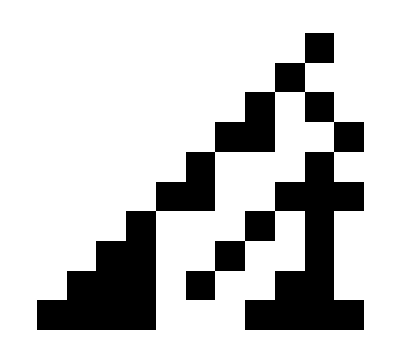

```mathematica
ArrayPlot@CellularAutomaton[MapThread[#:>Boole[Random[]<#2]&,{Tuples[{1,0},3],{1,.8,0,.3,.5,.44,1,.2}}],{{1},0},9]
```

## 17

### John Debrota

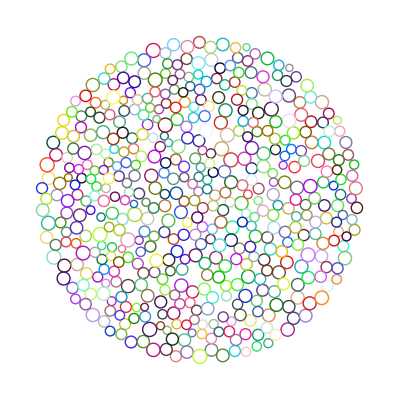

```mathematica
Graphics[{RandomColor[],#}&/@Insphere/@Module[{s=DiscretizeRegion@Disk[]},MeshCoordinates[s]⟦#⟧&/@#⟦1⟧&/@MeshCells[s,2]]]
```

## 18 Palindrome sentences in example data

### Kyle Keane

```mathematica
Select[ToLowerCase@StringReplace[Flatten[TextSentences/@ExampleData/@ExampleData@"Text"],Except@WordCharacter->""],PalindromeQ]
```

{,i,ii,iii,xix,xx,xxx,1,4,9,33,101,131,161,171,181,191,202,212,222,232,252,262,272,282,,,r,b,b,b,r,b,b,r,,,,,,uhu,,oho,p,p,p,p,p,tot,,,,â,,,,6,9,33,,,,,,,,,,m,m,a,,o,o,o,o,o,o,o,o,,,3,4,2,2,2,3,2,2,3,4,2,2,3,3,4,3,4,2,2,3,3,4,3,2,2,2,3,3,4,2,3,2,4,3,3,3,4,3,4,2,3,3,4,2,3,3,3,3,4,3,i,3,4,5,6,9,ii,3,4,3,3,4,v}

## 19 Sentences that are palindromes in wikipedia data, with some error handling

### Kyle Keane

```mathematica
Select[StringReplace[Flatten[TextSentences[WikipediaData@WordData[]/._Missing->Nothing]],Except@WordCharacter->""],PalindromeQ]
```

## 20 Date histogram of file types, when did you fully migrate to .nb?

### Kyle Keane

```mathematica
Quiet@DateHistogram@KeyValueMap[Tooltip[#2,Length@#2 #]&,FileDate/@#&/@KeyDrop[GroupBy[Import@$HomeDirectory,FileExtension],""]]
```

## 21 Paper Dolls

### Abby Brown

```mathematica
s=Sin;c=Cos;a=(t+s[2t]+s[4t]+s[6t])/6;b=.4(s@t+s[3t]+s[5t]+s[7t]);ParametricPlot3D[{c@a(9+c@b),(9+c@b)s@a,9-3s@b},{t,0,12Pi}]
```

-Graphics3D-

## 22 Kites

### Abby Brown

```mathematica
Animate[ParametricPlot[{t+2 Sin[t]+Sin[4 t],Sin[t]+Sin[3 t]+Sin[5 t]},{t,0,p},PlotRange->{{0,26},{-3,3}},Axes->None],{p,.1,27}]
```

## 23 A SE legacy re-imagined as a self-triggering dynamic

### George Varnavides

```mathematica
{v,p}=RandomPoint[Ball[],#]&/@{1500,15000};
n=Nearest@v
f=0.9975 (#1+0.01 (#1-#2))&
Dynamic@Graphics3D@Point[p=f[p,First/@n/@p]]
```

NearestFunction[{3, <>}]

0.9975 (#1+0.01 (#1-#2))&

-Graphics3D-

## 24 Symmetry in Chaos

### George Varnavides

```mathematica
c=#*
ArrayPlot@Log[BinCounts[Through@{Re,Im}@#&/@NestList[(5 # c+Re@#^6-2.7)# + c^5&,.1+.2I,9^7],a={-1,1,0.001},a]+1]
```

Conjugate[#1]

-Graphics-

## 25 Projections

### Stephan Leibbrandt

```mathematica
CountryData["World",{"Shape",#}]⟦1,3,1⟧&/@{"Orthographic","Mercator"};
Animate[Graphics[{Polygon[%⟦1⟧+f(%⟦2⟧-%⟦1⟧)]}],{f,0,.04}]
```

## 26 Electrical Engineering Application: Effective Impedance

### Stephan Leibbrandt

After evaluation, enter into the input field a network of resistances R, capacities C and inductances L. The element type and its value are separated by ^. Parallel elements or subnetworks are separated by ||, while && separates those in series. A subnetwork can be grouped with parentheses or the operator precedence of && and || controls the grouping. When you leave the field, the effective impedance is shown to the right.

Enter for example R^r1||R^r2&&R^r3 or R^r2||L^l1||(R^r1&&C^c1) and leave the field.

```mathematica
d=Dynamic;InputField@d@n->d@FullSimplify[ n//.{R^r_:>r,L^l_:>I*ω*l,C^c_:>1/I/ω/c}//.{f_∨s_∨r___:>f*s/(f+s)∨r,f_∧s_∧r___:>f+s∧r}]
```

→(l1 r2 ω (-ⅈ+c1 r1 ω))/(-r2-ⅈ (l1+c1 r1 r2) ω+c1 l1 (r1+r2) ω^2)

## 27 Medical Application: Neuropsychology

### Stephan Leibbrandt

The short term memory is often affected after a stroke and can be trained with the following application.

An Image is shown and the patient should decide, if it was already shown a certain number of steps before. Here, there are three steps from one image to the next, i.e. two images are in between. The number of steps as well as the number of different images control the difficulty of the task. Here, a span of five images is selected in order to have a reasonable amount of positives and to give higher weight for the similar looking images, here Venus and Mars. Lack of more characters for coding, the operating point of difficulty is not variable, but fixed by the given images.

A test starts by hitting either the “Not” or the “Or” button below and causes the display of an image on the left and the number of wrong as well as total guesses right of the two buttons. The next three hits on either button only proceed in the image sequence and cannot increase the number of wrong guesses, because there were not enough images shown yet to compare. Now, the test starts.

If an image was shown exactly three steps before (two images in between), the “Or” button is the correct choice. Otherwise, hit the “Not” button. All succeeding hits count for the test until literal False is shown instead of the image: there were as many guesses as images (the first three are always correct). Here, 33 images are used, i. e. the patient has 30 real trials. After no more image is shown, hitting the buttons does not make sense.

A standardization of step numbers and images would allow for a diagnosis of a patient.

```mathematica
l=PlanetData[All,"Image"]⟦;;5⟧~RandomChoice~33;
i=e=0;
Dynamic[i<34∧l⟦i⟧->ButtonBar[#:>#[l⟦i⟧≠l⟦++i-4⟧]∧i>4∧++e&/@{Not,Or}]|e|i]
```

-Graphics-→Not | Or|0|1

## 28 Portrait Maker

### Kyunghoon Kim

The length of text limitation is a big problem. But it’s fun time to me.

```mathematica
a = Entity["Person","StephenWolfram::j276d"]["Image"];
Show[Inpaint[a,ImageAdjust[CornerFilter[EdgeDetect[a],0.7]]],RemoveBackground[a,Pink]]
```

-Graphics-

## 29

### David Debrota

```mathematica
Colorize@MorphologicalComponents@SkeletonTransform@Dilation[Erosion[Image[Partition[RealDigits[E,2,12^6][[1]],12^3]],1],11]
```

-Graphics-

## 30

### Richard Scott

You don’t need a program to count to one million with this two minute self timer, but just in case:

```mathematica
Speak@Echo[StringJoin@@Thread[{ToString/@Accumulate[Flatten@{1,Table[10^i,{i,0,4},9]}//Join[#,Table[10^5,8],Reverse[#]]&]," "}]]
```

## 31

### Amy Friedman

As the work of Nobel laureates always proves highly influential, it goes without saying that Wolfram Research will be devoting substantial time in the near future to the nascent field of Bob Dylan Data Analytics. Herein, my contribution, The Song Titles. 
It goes, though, with saying that I started teaching myself how to code in the Wolfram Language yesterday, after breakfast, with the full encouragement of my son, and aided solely by Stephen Wolfram’s Introduction to the Wolfram Language.

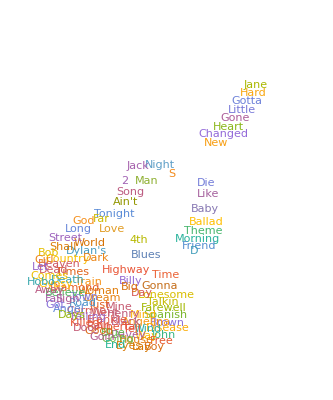

```mathematica
WordCloud[Import["http://www.angelfire.com/on/dylan/songlist.html"],Binarize[Import["http://bit.ly/2eq3A4r"]]]
```

## 32

### Mengxi Wu

```mathematica
SphericalPlot3D[1,u,v,MeshFunctions->{Sin[10(#4+#5)]&},Mesh->{{0.2}},PlotPoints->50,MeshShading->{FaceForm[Red,Green],None}]
```

-Graphics3D-

## 33

### Aaron Brzowski

```mathematica
Export["pFirstGen.gif",
EntityValue[
EntityList[
EntityClass["Pokemon","GenerationI"]],"Image"]];
```

```mathematica
Import["pFirstGen.gif"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## 34 Face Projection

### Shishir Reddy, Alex Krotz

Notes: Requires 2 faces and a webcam. Projects one face onto another.

```mathematica
Dynamic[v=CurrentImage[];c=FindFaces@v;If[Length@c>1,ImageCompose[v,ImageTrim[v,c[[1]]],Mean@c[[2]]],v]]
```

## 35

### Mengxi Wu

```mathematica
SystemDialogInput["RecordSound"]/.{x__}:>Reverse[{x}]
```